## Initial derivation

```mathematica
Solve[(γ+I*k*U1)^2*c2^2+(γ+I*k*U2)^2*c1^2==0,γ]//Simplify
```

{{γ→(k (c2 U1-ⅈ c1 U2))/(c1+ⅈ c2)},{γ→-(k (c2 U1+ⅈ c1 U2))/(c1-ⅈ c2)}}

```mathematica
Solve[1/(c^2 k^2)-1/γ^2-1/(γ-k*u)^2==0,γ]
```

{{γ→1/2 (k u-√(4 c^2 k^2+k^2 u^2-4 √(c^4 k^4+c^2 k^4 u^2)))},{γ→1/2 (k u+√(4 c^2 k^2+k^2 u^2-4 √(c^4 k^4+c^2 k^4 u^2)))},{γ→1/2 (k u-√(4 c^2 k^2+k^2 u^2+4 √(c^4 k^4+c^2 k^4 u^2)))},{γ→1/2 (k u+√(4 c^2 k^2+k^2 u^2+4 √(c^4 k^4+c^2 k^4 u^2)))}}

```mathematica
Solve[(γ+I*k*U1)^2*Sqrt[(γ+I*k*U2)^2+c^2 k^2]+(γ+I*k*U2)^2*Sqrt[(γ+I*k*U1)^2+c^2 k^2]==0,γ]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γ→-1/2 ⅈ (k U1+√(4 c^2 k^2-4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2)+k U2)},{γ→1/2 ⅈ (-k U1+√(4 c^2 k^2-4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2)-k U2)},{γ→-1/2 ⅈ (k U1+√(4 c^2 k^2+4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2)+k U2)},{γ→1/2 ⅈ (-k U1+√(4 c^2 k^2+4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2)-k U2)}}

```mathematica
1/2 ⅈ (-k U1-k U2-√(4 c^2 k^2-4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2))
1/2 ⅈ (-k U1-k U2-√(4 c^2 k^2+4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2))
1/2 ⅈ (-k U1-k U2+√(4 c^2 k^2-4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2))
1/2 ⅈ (-k U1-k U2+√(4 c^2 k^2+4 √(c^2 k^4 (c^2+(U1-U2)^2))+k^2 (U1-U2)^2))
```

```mathematica
1/2  (-k U1*I-k U2*I+√(-4 c^2 k^2-k^2 (U1-U2)^2+4 √(c^2 k^4 (c^2+(U1-U2)^2))))
1/2  (-k U1*I-k U2*I+√(-4 c^2 k^2-k^2 (U1-U2)^2-4 √(c^2 k^4 (c^2+(U1-U2)^2))))
1/2  (-k U1*I-k U2*I-√(-4 c^2 k^2-k^2 (U1-U2)^2+4 √(c^2 k^4 (c^2+(U1-U2)^2))))
1/2  (-k U1*I-k U2*I-√(-4 c^2 k^2-k^2 (U1-U2)^2-4 √(c^2 k^4 (c^2+(U1-U2)^2))))
```

```mathematica
1/2  (-k U1*I-k U2*I)+√(- c^2 k^2-k^2/4(U1-U2)^2+ √(c^2 k^4 (c^2+(U1-U2)^2)))
1/2  (-k U1*I-k U2*I)+√(-c^2 k^2-k^2/4 (U1-U2)^2-√(c^2 k^4 (c^2+(U1-U2)^2)))
1/2  (-k U1*I-k U2*I)-√(- c^2 k^2-k^2/4 (U1-U2)^2+ √(c^2 k^4 (c^2+(U1-U2)^2)))
1/2  (-k U1*I-k U2*I)-√(- c^2 k^2-k^2/4(U1-U2)^2-√(c^2 k^4 (c^2+(U1-U2)^2)))
```

```mathematica
1/2  (-k U1*I-k U2*I)+k √(- c^2 -1/4(U1-U2)^2+ c √(c^2+(U1-U2)^2))
1/2  (-k U1*I-k U2*I)+k √(-c^2 -1/4 (U1-U2)^2-c √(c^2+(U1-U2)^2))
1/2  (-k U1*I-k U2*I)-k √(- c^2 -1/4 (U1-U2)^2+c √(c^2+(U1-U2)^2))
1/2  (-k U1*I-k U2*I)-k √(- c^2 -1/4(U1-U2)^2-c √(c^2+(U1-U2)^2))
```

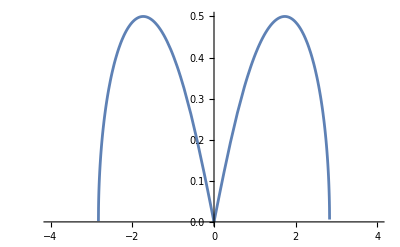

```mathematica
Plot[-I*Sqrt[(1+x^2/4)-Sqrt[1+x^2]],{x,-4,4}]
```

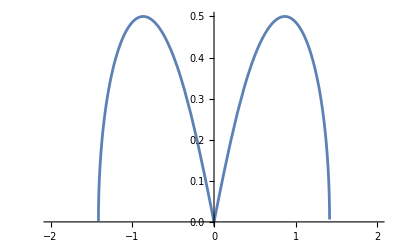

```mathematica
Plot[Sqrt[-(1+x^2)+Sqrt[1+4x^2]],{x,-2,2}]
```

```mathematica
Plot[-I*Sqrt[(1+x^2)-Sqrt[1+4x^2]],{x,-2,2}]
```

-Graphics-

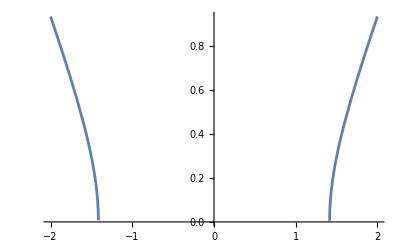

```mathematica
Plot[Sqrt[(1+x^2)-Sqrt[1+4x^2]],{x,-2,2}]
```

```mathematica
Plot[-I*Sqrt[(1+x^2)-Sqrt[1+4x^2]],{x,-2,2}]
```

-Graphics-

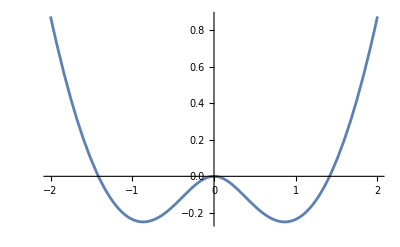

```mathematica
Plot[(1+x^2)-Sqrt[1+4x^2],{x,-2,2}]
```

```mathematica
Solve[1/(c^2 k^2)-1/γ^2-1/(γ-k*u)^2==0,γ]
```

{{γ→1/2 (k u-√(4 c^2 k^2+k^2 u^2-4 √(c^4 k^4+c^2 k^4 u^2)))},{γ→1/2 (k u+√(4 c^2 k^2+k^2 u^2-4 √(c^4 k^4+c^2 k^4 u^2)))},{γ→1/2 (k u-√(4 c^2 k^2+k^2 u^2+4 √(c^4 k^4+c^2 k^4 u^2)))},{γ→1/2 (k u+√(4 c^2 k^2+k^2 u^2+4 √(c^4 k^4+c^2 k^4 u^2)))}}

```mathematica
Limit[1/Subscript[c, 2]^2-1/Subscript[c, 1]^2+(Subscript[γ̄, 1]^2 (1+√(1+(4 Subscript[c, 1]^2 ((kx^2+Subscript[k, y]^2)Subscript[c, 1]^2+ Subscript[γ̄, 1]^2))/g^2)))/(2  Subscript[c, 1]^2 (Subscript[c, 1]^2 (Subscript[k, x]^2+Subscript[k, y]^2)+Subscript[γ̄, 1]^2))+(Subscript[γ̄, 2]^2 (-1+√(1+(4  Subscript[c, 2]^2((kx^2+ky^2)Subscript[c, 2]^2+ Subscript[γ̄, 2]^2))/g^2)))/(2  Subscript[c, 2]^2 (Subscript[c, 2]^2 (Subscript[k, x]^2+Subscript[k, y]^2)+Subscript[γ̄, 2]^2)),{Subscript[c, 1]->∞,Subscript[c, 2]->∞}]
```

0

```mathematica
1/Subscript[c, 2]^2-1/Subscript[c, 1]^2+(Subscript[γ̄, 1]^2 (1+√(1+(4 Subscript[c, 1]^2 ((kx^2+Subscript[k, y]^2)Subscript[c, 1]^2+ Subscript[γ̄, 1]^2))/g^2)))/(2  Subscript[c, 1]^2 (Subscript[c, 1]^2 (Subscript[k, x]^2+Subscript[k, y]^2)+Subscript[γ̄, 1]^2))+(Subscript[γ̄, 2]^2 (-1+√(1+(4  Subscript[c, 2]^2((kx^2+ky^2)Subscript[c, 2]^2+ Subscript[γ̄, 2]^2))/g^2)))/(2  Subscript[c, 2]^2 (Subscript[c, 2]^2 (Subscript[k, x]^2+Subscript[k, y]^2)+Subscript[γ̄, 2]^2))
```

```mathematica
(1/Subscript[c, 2]^2-1/Subscript[c, 1]^2)( Subscript[c^2, 2] Subscript[k, x])( Subscript[c^2, 1] )+  Subscript[γ̄, 1]^2 (  Subscript[c^2, 2]/g)+  Subscript[γ̄, 2]^2 ( Subscript[c^2, 1]/g)=0
```

```mathematica
(ρ2-ρ1 )Subscript[k, x] g+  Subscript[γ̄, 1]^2  ρ1+  Subscript[γ̄, 2]^2 ρ2 =0
```

```mathematica
A k g+  (γ+I*k *U1)^2 α1+  (γ+I*k *U2)^2 α2 =0
```

```mathematica
Solve[A k g+  (γ+I*k *U1)^2 α1+  (γ+I*k *U2)^2 α2 ==0,γ]//Simplify
```

{{γ→-(ⅈ (k U1 α1+k U2 α2-ⅈ √(k (k (U1-U2)^2 α1 α2-A g (α1+α2)))))/(α1+α2)},{γ→(-ⅈ k (U1 α1+U2 α2)+√(k (k (U1-U2)^2 α1 α2-A g (α1+α2))))/(α1+α2)}}

```mathematica
Collect[(k^2 c1^2+(γ+I*k*U1)^2)(γ+I*k*U2)^4 c1^2-(k^2 c2^2+(γ+I*k*U2)^2)(γ+I*k*U1)^4 c2^2==0,γ,Simplify]
```

k^6 (-c2^4 U1^4+c2^2 U1^4 U2^2+c1^2 (c1^2-U1^2) U2^4)-2 ⅈ k^5 (-2 c2^4 U1^3+c2^2 U1^3 U2 (U1+2 U2)+c1^2 U2^3 (2 c1^2-U1 (2 U1+U2))) γ+k^4 (6 c2^4 U1^2+c1^2 U2^2 (-6 c1^2+6 U1^2+8 U1 U2+U2^2)-c2^2 U1^2 (U1^2+8 U1 U2+6 U2^2)) γ^2+4 ⅈ k^3 (-c2^4 U1+c1^2 U2 (c1^2-U1^2-3 U1 U2-U2^2)+c2^2 U1 (U1^2+3 U1 U2+U2^2)) γ^3+k^2 (c1^4+c2^2 (-c2^2+6 U1^2+8 U1 U2+U2^2)-c1^2 (U1^2+8 U1 U2+6 U2^2)) γ^4+2 ⅈ k (-c2^2 (2 U1+U2)+c1^2 (U1+2 U2)) γ^5+(c1^2-c2^2) γ^6==0

```mathematica
Collect[(k^2 c1^2+(γ+I*k*U1)^2)^(1/2)(γ+I*k*U2)^2 c1^1+(k^2 c2^2+(γ+I*k*U2)^2)^(1/2)(γ+I*k*U1)^2 c2^1==0,γ,Simplify]
```

γ^2 (c1 √(c1^2 k^2+(ⅈ k U1+γ)^2)+c2 √(c2^2 k^2+(ⅈ k U2+γ)^2))+2 ⅈ k γ (c1 U2 √(c1^2 k^2+(ⅈ k U1+γ)^2)+c2 U1 √(c2^2 k^2+(ⅈ k U2+γ)^2))-k^2 (c1 U2^2 √(c1^2 k^2+(ⅈ k U1+γ)^2)+c2 U1^2 √(c2^2 k^2+(ⅈ k U2+γ)^2))==0

```mathematica
Solve[(k^2 c1^2+(γ+I*k*U1)^2)^(1/2)(γ-I*k*U1)^2 c1^1+(k^2 c2^2+(γ-I*k*U1)^2)^(1/2)(γ+I*k*U1)^2 c2^1==0,γ]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γ→(ⅈ (c1+c2) k U1)/(c1-c2)},{γ→(ⅈ (c1 k U1-c2 k U1))/(c1+c2)},{γ→-1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))-1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (-c1^2 k^2-c2^2 k^2-2 k^2 U1^2)-(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))-1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3)-(4 ⅈ (c1^2 k^3 U1-c2^2 k^3 U1))/(√(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))))},{γ→-1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (-c1^2 k^2-c2^2 k^2-2 k^2 U1^2)-(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))-1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3)-(4 ⅈ (c1^2 k^3 U1-c2^2 k^3 U1))/(√(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))))},{γ→1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))-1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (-c1^2 k^2-c2^2 k^2-2 k^2 U1^2)-(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))-1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3)+(4 ⅈ (c1^2 k^3 U1-c2^2 k^3 U1))/(√(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))))},{γ→1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/2 √(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (-c1^2 k^2-c2^2 k^2-2 k^2 U1^2)-(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))-1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3)+(4 ⅈ (c1^2 k^3 U1-c2^2 k^3 U1))/(√(-c1^2 k^2-c2^2 k^2-2 k^2 U1^2+1/3 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)+(2^(1/3) k^4 (c1^2+c2^2-4 U1^2)^2)/(3 (-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))+1/(3 2^(1/3))(-108 (c1^2 k^3 U1-c2^2 k^3 U1)^2+2 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2)^3-72 (c1^2 k^2+c2^2 k^2+2 k^2 U1^2) (-c1^2 k^4 U1^2-c2^2 k^4 U1^2+k^4 U1^4)+√(1728 c1^8 c2^2 k^12 U1^2+5184 c1^6 c2^4 k^12 U1^2+5184 c1^4 c2^6 k^12 U1^2+1728 c1^2 c2^8 k^12 U1^2-20736 c1^6 c2^2 k^12 U1^4+145152 c1^4 c2^4 k^12 U1^4-20736 c1^2 c2^6 k^12 U1^4+82944 c1^4 c2^2 k^12 U1^6+82944 c1^2 c2^4 k^12 U1^6-110592 c1^2 c2^2 k^12 U1^8))^(1/3))))}}

```mathematica
Collect[((c1/U1)^2+(γ+I)^2)(γ-I)^4 c1^2-((c2/U1)^2+(γ-I)^2)(γ+I)^4 c2^2,γ]
```

-c1^2+c2^2+c1^4/U1^2-c2^4/U1^2+(-2 ⅈ c1^2-2 ⅈ c2^2+(4 ⅈ c1^4)/U1^2+(4 ⅈ c2^4)/U1^2) γ+(-c1^2+c2^2-(6 c1^4)/U1^2+(6 c2^4)/U1^2) γ^2+(-4 ⅈ c1^2-4 ⅈ c2^2-(4 ⅈ c1^4)/U1^2-(4 ⅈ c2^4)/U1^2) γ^3+(c1^2-c2^2+c1^4/U1^2-c2^4/U1^2) γ^4+(-2 ⅈ c1^2-2 ⅈ c2^2) γ^5+(c1^2-c2^2) γ^6

```mathematica
Collect[((c1/U1)^2+(γ+I)^2)(γ-I)^4 c1^2-((c2/U1)^2+(γ-I)^2)(γ+I)^4 c2^2,γ,Simplify]
```

((c1^2-c2^2) (c1^2+c2^2-U1^2))/U1^2-(2 ⅈ (-2 c1^4-2 c2^4+c1^2 U1^2+c2^2 U1^2) γ)/U1^2+(-c1^2+c2^2-(6 c1^4)/U1^2+(6 c2^4)/U1^2) γ^2-(4 ⅈ (c1^4+c2^4+c1^2 U1^2+c2^2 U1^2) γ^3)/U1^2+((c1^2-c2^2) (c1^2+c2^2+U1^2) γ^4)/U1^2-2 ⅈ (c1^2+c2^2) γ^5+(c1^2-c2^2) γ^6

Divide by c1^2+c2^2, Note c1^2-c2^2/c1^2+c2^2 =A, Mc = 2U1/(c1+c2)

```mathematica
(A (c1^2+c2^2-U1^2))/U1^2-(2 ⅈ (-2( c1^4+ c2^4)/(c1^2+c2^2)+U1^2) γ)/U1^2+(-A-(6 (c1^2-c2^2))/U1^2) γ^2-(4 ⅈ ((c1^4+c2^4)/(c1^2+c2^2)+U1^2) γ^3)/U1^2+(A (c1^2+c2^2+U1^2) γ^4)/U1^2-2 ⅈ  γ^5+A γ^6
```

```mathematica
A((c1^2+c2^2)/U1^2-1)-((-2( c1^4+ c2^4)/(c1^2+c2^2))/U1^2+1)2 ⅈ γ+(-A-(12 (c1-c2))/(U1 Mc)) γ^2-(((c1^4+c2^4)/(c1^2+c2^2))/U1^2+1)4 ⅈ γ^3+((c1^2+c2^2)/U1^2+1)A γ^4-2 ⅈ  γ^5+A γ^6
```

```mathematica
A((c1^2+c2^2)/U1^2-1)-((-2( c1^4+ c2^4)/(U1^2(c1^2+c2^2))) +1)2 ⅈ γ+(-A-(12 (c1-c2))/(U1 Mc)) γ^2-((c1^4+c2^4)/(U1^2(c1^2+c2^2))+1)4 ⅈ γ^3+((c1^2+c2^2)/U1^2+1)A γ^4-2 ⅈ  γ^5+A γ^6
```

```mathematica
√(-(1+1/Mc^2)+2/Mc √(1+1/(4 Mc^2)))
```

```mathematica
Collect[(γ-√(-(1+1/Mc^2)+2/Mc √(1+1/(4 Mc^2))))(γ+√(-(1+1/Mc^2)+2/Mc √(1+1/(4 Mc^2))))(γ-√(-(1+1/Mc^2)-2/Mc √(1+1/(4 Mc^2))))(γ+√(-(1+1/Mc^2)-2/Mc √(1+1/(4 Mc^2)))),γ,Simplify]
```

1-2/Mc^2+(2+2/Mc^2) γ^2+γ^4

```mathematica
Simplify[(((c1/U1)^2+(γ+I)^2)(γ-I)^4 c1^2-((c2/U1)^2+(γ-I)^2)(γ+I)^4 c2^2)/((γ-(ⅈ (c1-c2))/(c1+c2))(γ-(ⅈ (c1+c2))/(c1-c2)))]
```

((c1-c2) (c1+c2) (c1^2 (-ⅈ+γ)^2+(ⅈ+γ)^2 (c2^2+U1^2 (-ⅈ+γ)^2)))/U1^2

```mathematica
Collect[c1^2 (-ⅈ+γ)^2+(ⅈ+γ)^2 (c2^2+U1^2 (-ⅈ+γ)^2),γ,Simplify]
```

-c1^2-c2^2+U1^2-2 ⅈ (c1^2-c2^2) γ+(c1^2+c2^2+2 U1^2) γ^2+U1^2 γ^4

```mathematica
-(c1^2+c2^2)+U1^2-2 ⅈ (c1^2-c2^2) γ+(c1^2+c2^2+2 U1^2) γ^2+U1^2 γ^4
```

```mathematica
(-(c1^2+c2^2))/U1^2+1-2 ⅈ (c1-c2)/(U1 Mc)γ+((c1^2+c2^2)/U1^2+2 ) γ^2+γ^4
```

```mathematica
Solve[(c1^2-c2^2)/(c1^2+c2^2)==A,c1]//Simplify
```

{{c1→-(√(-((1+A) c2^2)))/(√(-1+A))},{c1→(√(-((1+A) c2^2)))/(√(-1+A))}}

```mathematica
Solve[(c1^2-c2^2)/(c1^2+c2^2)==A,c2]//Simplify
```

{{c2→-(√(-((-1+A) c1^2)))/(√(1+A))},{c2→(√(-((-1+A) c1^2)))/(√(1+A))}}

```mathematica
c1==(√(1+A)c2)/(√(1-A)),c2==(√(1-A)c1)/(√(1+A))
```

```mathematica
Solve[(c2^2-c1^2)/(c1^2+c2^2)==A,c2]//Simplify
```

{{c2→-(√(-((1+A) c1^2)))/(√(-1+A))},{c2→(√(-((1+A) c1^2)))/(√(-1+A))}}

```mathematica
(i √((1+A) c1^2))/(i √(1-A))
```

```mathematica
ReplaceAll[(g c2)/(2 c1 d cost),c2->(√(1-A)c1)/(√(1+A))]
```

(√(1-A) g)/(2 √(1+A) cost d)

```mathematica
ReplaceAll[-(c1^2+c2^2)+U1^2-2 ⅈ (c1^2-c2^2) γ+(c1^2+c2^2+2 U1^2) γ^2+U1^2 γ^4,γ->-I*γ]
```

-c1^2-c2^2+U1^2-2 (c1^2-c2^2) γ-(c1^2+c2^2+2 U1^2) γ^2+U1^2 γ^4

```mathematica
-(c1^2+c2^2)/U1^2+1-2 (c1^2-c2^2)/U1^2 γ-((c1^2+c2^2)/U1^2+2 ) γ^2+ γ^4
```

```mathematica
-(c1^2+c2^2)/U1^2-2 (c1^2-c2^2)/U1^2 γ-(c1^2+c2^2)/U1^2 γ^2+1-2 γ^2  + γ^4
```

```mathematica
1/U1^2(-(c1^2+c2^2)-2 (c1^2-c2^2) γ-(c1^2+c2^2)γ^2)+1-2 γ^2  + γ^4
```

```mathematica
-(c1^2+c2^2)/U1^2(1+2 A γ+γ^2)+1-2 γ^2  + γ^4
```

```mathematica
-1/Mc2(1+2  A γ+γ^2)+(1-γ^2)^2
```

```mathematica
Collect[-1/Mc2(1+2  A γ+γ^2)+(1-γ^2)^2,γ]
```

1-1/Mc2-(2 A γ)/Mc2+(-2-1/Mc2) γ^2+γ^4

```mathematica
M-2 MA2 γ+(-3+M) γ^2+γ^4
```

```mathematica
Solve[M-2 MA2 γ+(-3+M) γ^2+γ^4==0,γ]//Simplify
```

{{γ→1/6 (-√3 √(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))-3 √(4-(4 M)/3-(3+M)^2/(3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))-1/3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)-(4 √3 MA2)/(√(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)))))},{γ→1/6 (-√3 √(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+3 √(4-(4 M)/3-(3+M)^2/(3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))-1/3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)-(4 √3 MA2)/(√(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)))))},{γ→1/6 (√3 √(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))-3 √(4-(4 M)/3-(3+M)^2/(3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))-1/3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)+(4 √3 MA2)/(√(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)))))},{γ→1/6 (√3 √(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+3 √(4-(4 M)/3-(3+M)^2/(3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))-1/3 ((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)+(4 √3 MA2)/(√(6-2 M+(3+M)^2/(((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3))+((-3+M)^3-36 (-3+M) M+54 MA2^2+1/2 √(-4 (3+M)^6+4 ((-3+M)^3-36 (-3+M) M+54 MA2^2)^2))^(1/3)))))}}

```mathematica
Simplify[-(1+c2^2/c1^2)-2 ⅈ (1-c2^2/c1^2) γ+(1+c2^2/c1^2)γ^2]
```

(c1^2 (-ⅈ+γ)^2+c2^2 (ⅈ+γ)^2)/c1^2

```mathematica
ReplaceAll[(c1+c2)/(2U),c2->(√(1-A)c1)/(√(1+A))]//Simplify
```

(c1+(√(1-A) c1)/(√(1+A)))/(2 U)

```mathematica
c1/(2U)(1+(√(1-A))/(√(1+A)))
```

```mathematica
Collect[((c1/U1)^2+(γ+I)^2)^(1/2)(γ-I)^2 c1+((c2/U1)^2+(γ-I)^2)^(1/2)(γ+I)^2 c2,γ,Simplify]
```

-c2 √(c2^2/U1^2+(-ⅈ+γ)^2)-c1 √(c1^2/U1^2+(ⅈ+γ)^2)+2 ⅈ γ (c2 √(c2^2/U1^2+(-ⅈ+γ)^2)-c1 √(c1^2/U1^2+(ⅈ+γ)^2))+γ^2 (c2 √(c2^2/U1^2+(-ⅈ+γ)^2)+c1 √(c1^2/U1^2+(ⅈ+γ)^2))

## KHI w/ B w/o g

```mathematica
Limit[ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ1),V->B/(√(μ*ρ1)),γ̄->(γ+I*kx*U1),L->(P/ρ1)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}],g->0,Direction->"FromAbove"]//Simplify
```

-√((B^2 (kx^2+ky^2) (2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1))-(kx U1-ⅈ γ)^2 μ ρ1 (ky^2 P+2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1)))/(-P (kx U1-ⅈ γ)^2 μ ρ1+B^2 (2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1))))

```mathematica
hminus=-√((V1^2 K^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))-(kx U1-ⅈ γ)^2  (ky^2 c1^2+2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2)))/(-c1^2 (kx U1-ⅈ γ)^2  +V1^2  (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))));
```

```mathematica
Limit[ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))+√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ2),V->B/(√(μ*ρ2)),γ̄->(γ+I*kx*U2),L->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}],g->0,Direction->"FromAbove"]//Simplify
```

√((B^2 (kx^2+ky^2) (2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2))-(kx U2-ⅈ γ)^2 μ ρ2 (ky^2 P+2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2)))/(-P (kx U2-ⅈ γ)^2 μ ρ2+B^2 (2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2))))

```mathematica
hplus=√((V2^2 K^2 (2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 ))-(kx U2-ⅈ γ)^2  (ky^2 c2^2+2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2)))/(-c2^2 (kx U2-ⅈ γ)^2  +V2^2  (2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 ))));
```

```mathematica
disp=ReplaceAll[-(hminus (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hplus (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))),{Subscript[c, 2]->√(P/ρ2),Subscript[V, 2]->B/(√(μ*ρ2)),Subscript[γ̄, 2]->(γ+I*kx*U2),Subscript[L, 2]->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2),Subscript[c, 1]->√(P/ρ1),Subscript[V, 1]->B/(√(μ*ρ1)),Subscript[γ̄, 1]->(γ+I*kx*U1),Subscript[L, 1]->(P/ρ1)/g}]//Simplify
```

1/μ((√(((kx^2+ky^2) V1^2 (c1^2 kx^2-(kx U1-ⅈ γ)^2)-c1^2 (kx^2+ky^2) (kx U1-ⅈ γ)^2+(kx U1-ⅈ γ)^4)/(V1^2 (c1^2 kx^2-(kx U1-ⅈ γ)^2)-c1^2 (kx U1-ⅈ γ)^2)) (-B^2 kx^2+(kx U1-ⅈ γ)^2 μ ρ1) (P (kx U1-ⅈ γ)^2 μ ρ1-B^2 (2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1))))/(B^2 (kx^2+ky^2) (2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1))-(kx U1-ⅈ γ)^2 μ ρ1 (ky^2 P+2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1)))+(√(((kx^2+ky^2) V2^2 (c2^2 kx^2-(kx U2-ⅈ γ)^2)-c2^2 (kx^2+ky^2) (kx U2-ⅈ γ)^2+(kx U2-ⅈ γ)^4)/(V2^2 (c2^2 kx^2-(kx U2-ⅈ γ)^2)-c2^2 (kx U2-ⅈ γ)^2)) (-B^2 kx^2+(kx U2-ⅈ γ)^2 μ ρ2) (P (kx U2-ⅈ γ)^2 μ ρ2-B^2 (2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2))))/(B^2 (kx^2+ky^2) (2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2))-(kx U2-ⅈ γ)^2 μ ρ2 (ky^2 P+2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2))))

```mathematica
((-V1^2 kx^2+(kx U1-ⅈ γ)^2 )  ρ1(c1^2 (kx U1-ⅈ γ)^2 -V1^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 )))^(1/2))/((V1^2 K^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))-(kx U1-ⅈ γ)^2 (ky^2 c1^2+2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 )))^(1/2))+ ((-V2^2 kx^2+(kx U2-ⅈ γ)^2)  ρ2(c2^2 (kx U2-ⅈ γ)^2 -V2^2 (2 ⅈ kx U2 γ +γ^2+kx^2 (c1^2-U2^2 )))^(1/2))/((V2^2 K^2 (2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 ))-(kx U2-ⅈ γ)^2  (ky^2 c2^2+2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 )))^(1/2))
```

```mathematica
Simplify[√((K^2 V1^2 (c1^2 kx^2-(kx U1-ⅈ γ)^2)-c1^2 (kx^2+ky^2) (kx U1-ⅈ γ)^2+(kx U1-ⅈ γ)^4)/(V1^2 (c1^2 kx^2-(kx U1-ⅈ γ)^2)-c1^2 (kx U1-ⅈ γ)^2))((-V1^2 kx^2+(kx U1-ⅈ γ)^2 )  ρ1(c1^2 (kx U1-ⅈ γ)^2 -V1^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))))/(V1^2 K^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))-(kx U1-ⅈ γ)^2 (ky^2 c1^2+2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 )))+√((K^2 V2^2 (c2^2 kx^2-(kx U2-ⅈ γ)^2)-c2^2 (kx^2+ky^2) (kx U2-ⅈ γ)^2+(kx U2-ⅈ γ)^4)/(V2^2 (c2^2 kx^2-(kx U2-ⅈ γ)^2)-c2^2 (kx U2-ⅈ γ)^2)) ((-V2^2 kx^2+(kx U2-ⅈ γ)^2)  ρ2(c2^2 (kx U2-ⅈ γ)^2 -V2^2 (2 ⅈ kx U2 γ +γ^2+kx^2 (c1^2-U2^2 ))))/(V2^2 K^2 (2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 ))-(kx U2-ⅈ γ)^2  (ky^2 c2^2+2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 )))]
```

((kx^2 (-U1^2+V1^2)+2 ⅈ kx U1 γ+γ^2) ρ1)/(√((K^2 V1^2 (c1^2 kx^2-(kx U1-ⅈ γ)^2)-c1^2 (kx^2+ky^2) (kx U1-ⅈ γ)^2+(kx U1-ⅈ γ)^4)/(V1^2 (c1^2 kx^2-(kx U1-ⅈ γ)^2)-c1^2 (kx U1-ⅈ γ)^2)))+((-kx^2 V2^2+(kx U2-ⅈ γ)^2) (-V2^2 (c1^2 kx^2-(kx U2-ⅈ γ)^2)+c2^2 (kx U2-ⅈ γ)^2) ρ2)/((V2^2 (c2^2 kx^2-(kx U2-ⅈ γ)^2)-c2^2 (kx U2-ⅈ γ)^2) √((K^2 V2^2 (c2^2 kx^2-(kx U2-ⅈ γ)^2)-c2^2 (kx^2+ky^2) (kx U2-ⅈ γ)^2+(kx U2-ⅈ γ)^4)/(V2^2 (c2^2 kx^2-(kx U2-ⅈ γ)^2)-c2^2 (kx U2-ⅈ γ)^2)))

```mathematica
ReplaceAll[((-V1^2 kx^2+(kx U1-ⅈ γ)^2 )  ρ1(c1^2 (kx U1-ⅈ γ)^2 -V1^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 )))^(1/2))/((V1^2 K^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))-(kx U1-ⅈ γ)^2 (ky^2 c1^2+2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 )))^(1/2))+ ((-V2^2 kx^2+(kx U2-ⅈ γ)^2)  ρ2(c2^2 (kx U2-ⅈ γ)^2 -V2^2 (2 ⅈ kx U2 γ +γ^2+kx^2 (c1^2-U2^2 )))^(1/2))/((V2^2 K^2 (2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 ))-(kx U2-ⅈ γ)^2  (ky^2 c2^2+2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 )))^(1/2)),{V1->V,V2->V,c1->c,c2->c,U2->-U1,ρ1->ρ,ρ2->ρ,ky->0,K->kx}]//Simplify
```

(-(√(-V^2 (c^2 kx^2-(kx U1+ⅈ γ)^2)+c^2 (kx U1+ⅈ γ)^2) √((c^2 kx^2-(kx U1+ⅈ γ)^2) (kx^2 (-U1^2+V^2)-2 ⅈ kx U1 γ+γ^2)))/(c^2 kx^2-(kx U1+ⅈ γ)^2)-(√(-V^2 (c^2 kx^2-(kx U1-ⅈ γ)^2)+c^2 (kx U1-ⅈ γ)^2) (kx^2 (-U1^2+V^2)+2 ⅈ kx U1 γ+γ^2))/(√((c^2 kx^2-(kx U1-ⅈ γ)^2) (kx^2 (-U1^2+V^2)+2 ⅈ kx U1 γ+γ^2)))) ρ

```mathematica
(√(-V^2 (c^2 kx^2-(kx U1+ⅈ γ)^2)+c^2 (kx U1+ⅈ γ)^2) √(kx^2 (-U1^2+V^2)-2 ⅈ kx U1 γ+γ^2))/(√(c^2 kx^2-(kx U1+ⅈ γ)^2))+(√(-V^2 (c^2 kx^2-(kx U1-ⅈ γ)^2)+c^2 (kx U1-ⅈ γ)^2) √(kx^2 (-U1^2+V^2)+2 ⅈ kx U1 γ+γ^2))/(√(c^2 kx^2-(kx U1-ⅈ γ)^2))
```

```mathematica
(√(-V^2 (c^2 kx^2-kx^2 U1^2(1+ⅈ γ)^2)+c^2 kx^2 U1^2(1+ⅈ γ)^2) √(kx^2 -U1^2+kx^2 V^2-2 ⅈ kx U1 γ+γ^2))/(√(c^2 kx^2-kx^2 U1^2(1+ⅈ γ)^2))+(√(-V^2 (c^2 kx^2-kx^2 U1^2(1-ⅈ γ)^2)+c^2 kx^2 U1^2(1-ⅈ γ)^2) √(kx^2 -U1^2+kx^2 V^2+2 ⅈ kx U1 γ+γ^2))/(√(c^2 kx^2-kx^2 U1^2(1-ⅈ γ)^2))
```

```mathematica
(√(-1/Ma^2(1/Mc^2 -(1+ⅈ γ)^2)+1/Mc^2 (1+ⅈ γ)^2) √(-1+1/Ma^2-2 ⅈ  γ+γ^2))/(√(1/Mc^2 -(1+ⅈ γ)^2))+(√(-1/Ma^2 (1/Mc^2 -(1-ⅈ γ)^2)+1/Mc^2 (1-ⅈ γ)^2) √(-1+1/Ma^2+2 ⅈ  γ+γ^2))/(√(1/Mc^2 -(1-ⅈ γ)^2))
```

```mathematica
(√(-1/Ma^2 1/Mc^2 +(1/Ma^2+1/Mc^2 )(1+ⅈ γ)^2) √(-1+1/Ma^2-2 ⅈ  γ+γ^2))/(√(1/Mc^2 -(1+ⅈ γ)^2))+(√(-1/Ma^2 1/Mc^2 +(1/Ma^2+1/Mc^2 )(1-ⅈ γ)^2) √(-1+1/Ma^2+2 ⅈ  γ+γ^2))/(√(1/Mc^2 -(1-ⅈ γ)^2))
```

```mathematica
Simplify[(√(-1/Ma^2 1/Mc^2 +(1/Ma^2+1/Mc^2 )(1+ⅈ γ)^2) √(-1+1/Ma^2-2 ⅈ  γ+γ^2))/(√(1/Mc^2 -(1+ⅈ γ)^2))+(√(-1/Ma^2 1/Mc^2 +(1/Ma^2+1/Mc^2 )(1-ⅈ γ)^2) √(-1+1/Ma^2+2 ⅈ  γ+γ^2))/(√(1/Mc^2 -(1-ⅈ γ)^2))]
```

(√((-1+(Ma^2+Mc^2) (1+ⅈ γ)^2)/(Ma^2 Mc^2)) √(1/Ma^2+(-ⅈ+γ)^2))/(√(1/Mc^2+(-ⅈ+γ)^2))+(√(1/Ma^2+(ⅈ+γ)^2) √(-(1+(Ma^2+Mc^2) (ⅈ+γ)^2)/(Ma^2 Mc^2)))/(√(1/Mc^2+(ⅈ+γ)^2))

```mathematica
(√(1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (-ⅈ+ γ)^2) √(1/Ma^2+(-ⅈ+γ)^2))/(√(1/Mc^2+(-ⅈ+γ)^2))+(√(1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (ⅈ+γ)^2)√(1/Ma^2+(ⅈ+γ)^2))/(√(1/Mc^2+(ⅈ+γ)^2))
```

```mathematica
Try squaring
```

```mathematica
((1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (-ⅈ+ γ)^2 )(1/Ma^2+(-ⅈ+γ)^2))/(1/Mc^2+(-ⅈ+γ)^2)-(( 1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (ⅈ+γ)^2)(1/Ma^2+(ⅈ+γ)^2))/(1/Mc^2+(ⅈ+γ)^2)
```

```mathematica
Together[((1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (-ⅈ+ γ)^2 )(1/Ma^2+(-ⅈ+γ)^2))/(1/Mc^2+(-ⅈ+γ)^2)-(( 1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (ⅈ+γ)^2)(1/Ma^2+(ⅈ+γ)^2))/(1/Mc^2+(ⅈ+γ)^2)]//Simplify
```

-(4 ⅈ γ (2+2 Mc^2 (-1+γ^2)+Mc^4 (1+γ^2)^2+Ma^2 (2 (-1+γ^2)+Mc^2 (1+γ^2)^2)))/(Ma^2 (1+Mc^2 (-ⅈ+γ)^2) (1+Mc^2 (ⅈ+γ)^2))

```mathematica
Collect[(2+2 Mc^2 (-1+γ^2)+Mc^4 (1+γ^2)^2+Ma^2 (2 (-1+γ^2)+Mc^2 (1+γ^2)^2)),γ,Simplify]
```

2-2 Mc^2+Mc^4+Ma^2 (-2+Mc^2)+2 (1+Mc^2) (Ma^2+Mc^2) γ^2+Mc^2 (Ma^2+Mc^2) γ^4

```mathematica
2-2 Mc^2+Mc^4-2 Ma^2 +Ma^2 Mc^2+2 (1+Mc^2) (Ma^2+Mc^2) γ^2+Mc^2 (Ma^2+Mc^2) γ^4
```

```mathematica
2-2 Mc^2+Mc^4-2 Ma^2 +Ma^2 Mc^2+2 (1+Mc^2) (Ma^2+Mc^2) γ^2+Mc^2 (Ma^2+Mc^2) γ^4
```

```mathematica
2-2 Mc^2-2 Ma^2 +Ma^2 Mc^2+Mc^4+2 (1+Mc^2) (Ma^2+Mc^2) γ^2+Mc^2 (Ma^2+Mc^2) γ^4
```

```mathematica
2-2 (Mc^2+Ma^2) +Mc^2(Ma^2 +Mc^2)+2 (1+Mc^2) (Ma^2+Mc^2) γ^2+Mc^2 (Ma^2+Mc^2) γ^4
```

```mathematica
2/Mt^2+(-2  +Mc^2)+2 (1+Mc^2)  γ^2+Mc^2  γ^4
```

```mathematica
Solve[2/Mt^2+(-2  +Mc^2)+2 (1+Mc^2)  γ+Mc^2  γ^2==0,γ]//Simplify
```

{{γ→-((1+Mc^2) Mt+√(Mt^2+Mc^2 (-2+4 Mt^2)))/(Mc^2 Mt)},{γ→(-((1+Mc^2) Mt)+√(Mt^2+Mc^2 (-2+4 Mt^2)))/(Mc^2 Mt)}}

```mathematica
-(1+1/Mc^2) +(√(Mt^2+Mc^2 (-2+4 Mt^2)))/(Mc^2 Mt)
```

```mathematica
-(1+1/Mc^2) +1/Mc √(1/Mc^2+(Mc^2 (-2+4 Mt^2))/(Mc^2 Mt^2))
```

```mathematica
-(1+1/Mc^2) +1/Mc √(1/Mc^2+(-2+4 Mt^2)/Mt^2)
```

```mathematica
-(1+1/Mc^2) +1/Mc √(1/Mc^2+-2/Mt^2+(4 Mt^2)/Mt^2)
```

```mathematica
-(1+1/Mc^2) +1/Mc √(1/Mc^2+-2/Mt^2+4)
```

```mathematica
-(1+1/Mc^2) +2/Mc √(1+1/(4 Mc^2)-1/(2 Mt^2))
```

```mathematica
Solve[(-2  +Mc^2)+2 (1+Mc^2)  γ+Mc^2  γ^2==0,γ]//Simplify
```

{{γ→-(1+Mc^2+√(1+4 Mc^2))/Mc^2},{γ→(-1-Mc^2+√(1+4 Mc^2))/Mc^2}}

```mathematica
Solve[(√(1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (-ⅈ+ γ)^2) √(1/Ma^2+(-ⅈ+γ)^2))/(√(1/Mc^2+(-ⅈ+γ)^2))+(√(1/(Ma^2 Mc^2)+(1/Mc^2+1/Ma^2) (ⅈ+γ)^2)√(1/Ma^2+(ⅈ+γ)^2))/(√(1/Mc^2+(ⅈ+γ)^2))==0,γ]
```

$Aborted

## KHI w/ B w/o g redo

```mathematica
Limit[ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ1),V->B/(√(μ*ρ1)),γ̄->(γ+I*kx*U1),L->(P/ρ1)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}],g->0,Direction->"FromAbove"]//Simplify
```

-√((B^2 (kx^2+ky^2) (2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1))-(kx U1-ⅈ γ)^2 μ ρ1 (ky^2 P+2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1)))/(-P (kx U1-ⅈ γ)^2 μ ρ1+B^2 (2 ⅈ kx U1 γ ρ1+γ^2 ρ1+kx^2 (P-U1^2 ρ1))))

```mathematica
hminus=-√((V1^2 K^2 (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))-(kx U1-ⅈ γ)^2  (ky^2 c1^2+2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2)))/(-c1^2 (kx U1-ⅈ γ)^2  +V1^2  (2 ⅈ kx U1 γ +γ^2 +kx^2 (c1^2-U1^2 ))));
```

```mathematica
hminus=-√((V1^2 K^2 (Subscript[γ̄, 1]^2+kx^2 c1^2 )+Subscript[γ̄, 1]^2  (Subscript[γ̄, 1]^2+kx^2 c1^2 ))/(c1^2 Subscript[γ̄, 1]^2  +V1^2  (Subscript[γ̄, 1]^2+kx^2 c1^2 )));
```

```mathematica
hminus=-√(((Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )(Subscript[V, 1]^2 K^2 +Subscript[γ̄, 1]^2 ))/(Subscript[c, 1]^2 Subscript[γ̄, 1]^2  +Subscript[V, 1]^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )));
```

Equal densities

```mathematica
hminus=-√(((Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )(V^2 K^2 +Subscript[γ̄, 1]^2 ))/(c^2 Subscript[γ̄, 1]^2  +V^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )));
```

```mathematica
Limit[ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))+√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ2),V->B/(√(μ*ρ2)),γ̄->(γ+I*kx*U2),L->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}],g->0,Direction->"FromAbove"]//Simplify
```

√((B^2 (kx^2+ky^2) (2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2))-(kx U2-ⅈ γ)^2 μ ρ2 (ky^2 P+2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2)))/(-P (kx U2-ⅈ γ)^2 μ ρ2+B^2 (2 ⅈ kx U2 γ ρ2+γ^2 ρ2+kx^2 (P-U2^2 ρ2))))

```mathematica
hplus=√((V2^2 K^2 (2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 ))-(kx U2-ⅈ γ)^2  (ky^2 c2^2+2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2)))/(-c2^2 (kx U2-ⅈ γ)^2  +V2^2  (2 ⅈ kx U2 γ +γ^2 +kx^2 (c2^2-U2^2 ))));
```

```mathematica
hplus=√((V2^2 K^2 ((ⅈ kx U2+ γ)^2+kx^2 c2^2 )+(I*kx U2+γ)^2  ((ⅈ kx U2+ γ)^2+kx^2 c2^2 ))/(c2^2 (I*kx U2+γ)^2  +V2^2  ((ⅈ kx U2+ γ)^2+kx^2 c2^2 )));
```

```mathematica
hplus=√((V2^2 K^2 (Subscript[γ̄, 2]^2+kx^2 c2^2 )+Subscript[γ̄, 2]^2  (Subscript[γ̄, 2]^2+kx^2 c2^2 ))/(c2^2 Subscript[γ̄, 2]^2 +V2^2  (Subscript[γ̄, 2]^2+kx^2 c2^2 )));
```

```mathematica
hplus=√(((Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )(Subscript[V, 2]^2 K^2 +Subscript[γ̄, 2]^2 ))/(c2^2 Subscript[γ̄, 2]^2 +Subscript[V, 2]^2  (Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )));
```

Equal densities

```mathematica
hplus=√(((Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 )(V^2 K^2 +Subscript[γ̄, 2]^2 ))/(c^2 Subscript[γ̄, 2]^2 +V^2  (Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 )));
```

Repeat for ease of access

```mathematica
hminus=-√(((Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )(V^2 K^2 +Subscript[γ̄, 1]^2 ))/(c^2 Subscript[γ̄, 1]^2  +V^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )));
```

```mathematica
disp=ReplaceAll[-(hm (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hp (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))),{Subscript[c, 2]->√(P/ρ2),Subscript[c, 1]->√(P/ρ1)}]//Simplify
```

(((B^2 P k_x^2+(B^2+P μ) ρ1 (γ̄)_1^2) √(((K^2 V_1^2+(γ̄)_1^2) (P k_x^2+ρ1 (γ̄)_1^2))/(P k_x^2 V_1^2+(P+ρ1 V_1^2) (γ̄)_1^2)) (k_x^2 k_y^2 V_1^4+K^2 V_1^2 (γ̄)_1^2+(γ̄)_1^4))/(K^2 P k_x^2 k_y^2 V_1^4+(γ̄)_1^2 (K^2 V_1^2+(γ̄)_1^2) (K^2 P+ρ1 k_y^2 V_1^2+ρ1 (γ̄)_1^2))+((B^2 P k_x^2+(B^2+P μ) ρ2 (γ̄)_2^2) √(((K^2 V_2^2+(γ̄)_2^2) (P k_x^2+ρ2 (γ̄)_2^2))/(P k_x^2 V_2^2+ρ2 (c2^2+V_2^2) (γ̄)_2^2)) (k_x^2 k_y^2 V_2^4+K^2 V_2^2 (γ̄)_2^2+(γ̄)_2^4))/(K^2 P k_x^2 k_y^2 V_2^4+(γ̄)_2^2 (K^2 V_2^2+(γ̄)_2^2) (K^2 P+ρ2 k_y^2 V_2^2+ρ2 (γ̄)_2^2)))/μ

```mathematica
-(hm μ Subscript[ρ, 1](Subscript[V, 1]^2 Subscript[c, 1]^2 Subscript[k, x]^2+(Subscript[V, 1]^2+Subscript[c, 1]^2 ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hp μ Subscript[ρ, 2](Subscript[V, 2]^2 Subscript[c, 2]^2 Subscript[k, x]^2+(Subscript[V, 2]^2+Subscript[c, 2]^2) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))
```

```mathematica
-(hm  Subscript[ρ, 1](Subscript[V, 1]^2 Subscript[c, 1]^2 Subscript[k, x]^2+(Subscript[V, 1]^2+Subscript[c, 1]^2 ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))+(hp  Subscript[ρ, 2](Subscript[V, 2]^2 Subscript[c, 2]^2 Subscript[k, x]^2+(Subscript[V, 2]^2+Subscript[c, 2]^2) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))
```

```mathematica
ReplaceAll[-(hm  Subscript[ρ, 1](Subscript[V, 1]^2 Subscript[c, 1]^2 Subscript[k, x]^2+(Subscript[V, 1]^2+Subscript[c, 1]^2 ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))+(hp  Subscript[ρ, 2](Subscript[V, 2]^2 Subscript[c, 2]^2 Subscript[k, x]^2+(Subscript[V, 2]^2+Subscript[c, 2]^2) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)),K->√(Subscript[k, x]^2+Subscript[k, y]^2)]//Simplify
```

-(hm ρ_1 (k_x^2 V_1^2+(γ̄)_1^2) (V_1^2 (γ̄)_1^2+c_1^2 (k_x^2 V_1^2+(γ̄)_1^2)))/(c_1^2 (k_x^2+k_y^2) (k_x^2 V_1^2+(γ̄)_1^2)+(γ̄)_1^2 (k_x^2 V_1^2+k_y^2 V_1^2+(γ̄)_1^2))+(hp ρ_2 (k_x^2 V_2^2+(γ̄)_2^2) (V_2^2 (γ̄)_2^2+c_2^2 (k_x^2 V_2^2+(γ̄)_2^2)))/(c_2^2 (k_x^2+k_y^2) (k_x^2 V_2^2+(γ̄)_2^2)+(γ̄)_2^2 (k_x^2 V_2^2+k_y^2 V_2^2+(γ̄)_2^2))

Same densities

```mathematica
-(hm (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2) (V^2 Subscript[γ̄, 1]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2)))/(c^2 (Subscript[k, x]^2+Subscript[k, y]^2) (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2)+Subscript[γ̄, 1]^2 (Subscript[k, x]^2 V^2+Subscript[k, y]^2 V^2+Subscript[γ̄, 1]^2))+(hp  (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2) (V^2 Subscript[γ̄, 2]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2)))/(c^2 (Subscript[k, x]^2+Subscript[k, y]^2) (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2)+Subscript[γ̄, 2]^2 (Subscript[k, x]^2 V^2+Subscript[k, y]^2 V^2+Subscript[γ̄, 2]^2))
```

ky = 0

```mathematica
-(hm (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2) (V^2 Subscript[γ̄, 1]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2)))/(c^2 Subscript[k, x]^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2)+Subscript[γ̄, 1]^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2))+(hp  (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2) (V^2 Subscript[γ̄, 2]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2)))/(c^2 Subscript[k, x]^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2)+Subscript[γ̄, 2]^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2))
```

```mathematica
-(hm (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2) (V^2 Subscript[γ̄, 1]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2)))/((Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2)(c^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))+(hp  (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2) (V^2 Subscript[γ̄, 2]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2)))/((Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2)(c^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))
```

```mathematica
-(hm  (V^2 Subscript[γ̄, 1]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 1]^2)))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )+(hp  (V^2 Subscript[γ̄, 2]^2+c^2 (Subscript[k, x]^2 V^2+Subscript[γ̄, 2]^2)))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )
```

```mathematica
-(hm  (V^2 Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2 V^2+c^2 Subscript[γ̄, 1]^2))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )+(hp  (V^2 Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 V^2+c^2 Subscript[γ̄, 2]^2))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )
```

```mathematica
-(hm  (V^2 (Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2)+c^2 Subscript[γ̄, 1]^2))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )+(hp  (V^2 (Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 )+c^2 Subscript[γ̄, 2]^2))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )
```

```mathematica
-(hm  (c^2 Subscript[γ̄, 1]^2+V^2 (Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2)))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )+(hp  (c^2 Subscript[γ̄, 2]^2+V^2 (Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 )))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )
```

Sub in h’s

```mathematica
√(((Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )(V^2 K^2 +Subscript[γ̄, 1]^2 ))/(c^2 Subscript[γ̄, 1]^2  +V^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )))(c^2 Subscript[γ̄, 1]^2+V^2 (Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )+√(((Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 )(V^2 K^2 +Subscript[γ̄, 2]^2 ))/(c^2 Subscript[γ̄, 2]^2 +V^2  (Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 )))(c^2 Subscript[γ̄, 2]^2+V^2 (Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 ))/(c^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )
```

```mathematica
√(((c^2 Subscript[γ̄, 1]^2+V^2 (Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))/(Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 ))+√(((c^2 Subscript[γ̄, 2]^2+V^2 (Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 ))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))/(Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 ))
```

Move to one side and square both sides then move back

```mathematica
((c^2 Subscript[γ̄, 1]^2+V^2 (Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))/(Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )-((c^2 Subscript[γ̄, 2]^2+V^2 (Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 ))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))/(Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 )
```

```mathematica
(c^2 Subscript[γ̄, 1]^2+V^2 (Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )(Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 )-(c^2 Subscript[γ̄, 2]^2+V^2 (Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 ))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ) (Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )
```

```mathematica
ReplaceAll[((c^2 Subscript[γ̄, 1]^2+V^2 (Subscript[γ̄, 1]^2+c^2 Subscript[k, x]^2))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))/(Subscript[γ̄, 1]^2+Subscript[k, x]^2 c^2 )-((c^2 Subscript[γ̄, 2]^2+V^2 (Subscript[γ̄, 2]^2+c^2 Subscript[k, x]^2 ))(V^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))/(Subscript[γ̄, 2]^2+Subscript[k, x]^2 c^2 ),{Subscript[γ̄, 1]->(γ+I*Subscript[k, x]*U),Subscript[γ̄, 2]->(γ-I*Subscript[k, x]*U)}]
```

-((V^2 k_x^2+(γ-ⅈ U k_x)^2) (c^2 (γ-ⅈ U k_x)^2+V^2 (c^2 k_x^2+(γ-ⅈ U k_x)^2)))/(c^2 k_x^2+(γ-ⅈ U k_x)^2)+((V^2 k_x^2+(γ+ⅈ U k_x)^2) (c^2 (γ+ⅈ U k_x)^2+V^2 (c^2 k_x^2+(γ+ⅈ U k_x)^2)))/(c^2 k_x^2+(γ+ⅈ U k_x)^2)

```mathematica
((V^2 Subscript[k, x]^2+ U^2 Subscript[k, x]^2(γ+ⅈ)^2) (c^2  U^2 Subscript[k, x]^2(γ+ⅈ )^2+V^2 (c^2 Subscript[k, x]^2+ U^2 Subscript[k, x]^2(γ+ⅈ )^2)))/(c^2 Subscript[k, x]^2+ U^2 Subscript[k, x]^2(γ+ⅈ )^2)-((V^2 Subscript[k, x]^2+ U^2 Subscript[k, x]^2(γ-ⅈ )^2) (c^2  U^2 Subscript[k, x]^2(γ-ⅈ )^2+V^2 (c^2 Subscript[k, x]^2+ U^2 Subscript[k, x]^2(γ-ⅈ )^2)))/(c^2 Subscript[k, x]^2+ U^2 Subscript[k, x]^2(γ-ⅈ )^2)
```

```mathematica
(U^2 Subscript[k, x]^2(V^2/U^2 +(γ+ⅈ)^2) (c^2  U^2 Subscript[k, x]^2(γ+ⅈ )^2+V^2 U^2 Subscript[k, x]^2(c^2/U^2 + (γ+ⅈ )^2)))/(c^2/U^2 + (γ+ⅈ )^2)-(U^2 Subscript[k, x]^2(V^2/U^2+ (γ-ⅈ )^2) (c^2  U^2 Subscript[k, x]^2(γ-ⅈ )^2+V^2 U^2 Subscript[k, x]^2(c^2/U^2 + (γ-ⅈ )^2)))/(c^2/U^2 +(γ-ⅈ )^2)
```

```mathematica
((V^2/U^2 +(γ+ⅈ)^2) (c^2  (γ+ⅈ )^2+V^2 (c^2/U^2 + (γ+ⅈ )^2)))/(c^2/U^2 + (γ+ⅈ )^2)-((V^2/U^2+ (γ-ⅈ )^2) (c^2  (γ-ⅈ )^2+V^2 (c^2/U^2 + (γ-ⅈ )^2)))/(c^2/U^2 +(γ-ⅈ )^2)
```

```mathematica
((V^2/U^2 +(γ+ⅈ)^2) (c^2/U^2  (γ+ⅈ )^2+V^2/U^2(c^2/U^2 + (γ+ⅈ )^2)))/(c^2/U^2 + (γ+ⅈ )^2)-((V^2/U^2+ (γ-ⅈ )^2) (c^2/U^2  (γ-ⅈ )^2+V^2/U^2 (c^2/U^2 + (γ-ⅈ )^2)))/(c^2/U^2 +(γ-ⅈ )^2)
```

```mathematica
((1/Ma^2 +(γ+ⅈ)^2) (1/Mc^2  (γ+ⅈ )^2+1/Ma^2(1/Mc^2 + (γ+ⅈ )^2)))/(1/Mc^2 + (γ+ⅈ )^2)-((1/Ma^2+ (γ-ⅈ )^2) (1/Mc^2  (γ-ⅈ )^2+1/Ma^2(1/Mc^2 + (γ-ⅈ )^2)))/(1/Mc^2 +(γ-ⅈ )^2)
```

```mathematica
((1/Ma^2 +(γ+ⅈ)^2) (1/Mc^2  (γ+ⅈ )^2+1/Ma^2 1/Mc^2 +1/Ma^2 (γ+ⅈ )^2))/(1/Mc^2 + (γ+ⅈ )^2)-((1/Ma^2+ (γ-ⅈ )^2) (1/Mc^2  (γ-ⅈ )^2+1/Ma^2 1/Mc^2 + 1/Ma^2(γ-ⅈ )^2))/(1/Mc^2 +(γ-ⅈ )^2)
```

```mathematica
((1/Ma^2 +(γ+ⅈ)^2) (1/Ma^2 1/Mc^2 +(1/Ma^2 +1/Mc^2  )(γ+ⅈ )^2))/(1/Mc^2 + (γ+ⅈ )^2)-((1/Ma^2+ (γ-ⅈ )^2) (1/Ma^2 1/Mc^2 + (1/Ma^2 +1/Mc^2  )(γ-ⅈ )^2))/(1/Mc^2 +(γ-ⅈ )^2)
```

```mathematica
(1/Ma^2 +(γ+ⅈ)^2) (1/Ma^2 1/Mc^2 +(1/Ma^2 +1/Mc^2  )(γ+ⅈ )^2)(1/Mc^2 +(γ-ⅈ )^2)-(1/Ma^2+ (γ-ⅈ )^2) (1/Ma^2 1/Mc^2 + (1/Ma^2 +1/Mc^2  )(γ-ⅈ )^2)(1/Mc^2 + (γ+ⅈ )^2)
```

```mathematica
Collect[ (1/Ma^2 +(γ+ⅈ)^2) (1/Ma^2 1/Mc^2 +(1/Ma^2 +1/Mc^2  )(γ+ⅈ )^2)(1/Mc^2 +(γ-ⅈ )^2)-(1/Ma^2+ (γ-ⅈ )^2) (1/Ma^2 1/Mc^2 + (1/Ma^2 +1/Mc^2  )(γ-ⅈ )^2)(1/Mc^2 + (γ+ⅈ )^2),γ,Simplify]
```

(4 ⅈ (2-2 Mc^2+Mc^4+Ma^2 (-2+Mc^2)) γ)/(Ma^2 Mc^4)+(8 ⅈ (1+Mc^2) (Ma^2+Mc^2) γ^3)/(Ma^2 Mc^4)+4 ⅈ (1/Ma^2+1/Mc^2) γ^5

```mathematica
(2-2 Mc^2+Mc^4+Ma^2 (-2+Mc^2))/(Ma^2 Mc^4)+(2  (1+Mc^2) (Ma^2+Mc^2) γ^2)/(Ma^2 Mc^4)+ (1/Ma^2+1/Mc^2) γ^4
```

```mathematica
(2-2 Mc^2+Mc^4-2 Ma^2+Ma^2 Mc^2)/(Ma^2 Mc^4)+(2  (1+Mc^2) (Ma^2+Mc^2) γ^2)/(Ma^2 Mc^4)+ ((Mc^2+Ma^2)/(Ma^2 Mc^2)) γ^4
```

```mathematica
(2-2 Mc^2+Mc^4-2 Ma^2+Ma^2 Mc^2)/Mc^2+(2  (1+Mc^2) (Ma^2+Mc^2) γ^2)/Mc^2+ (Mc^2+Ma^2) γ^4
```

```mathematica
(2-2 Mc^2-2 Ma^2+Mc^4+Ma^2 Mc^2)/Mc^2+(2  (1+Mc^2) (Ma^2+Mc^2) γ^2)/Mc^2+ (Mc^2+Ma^2) γ^4
```

```mathematica
(2+(Mc^2-2)( Mc^2+Ma^2))/Mc^2+(2  (1+Mc^2) (Ma^2+Mc^2) γ^2)/Mc^2+ (Mc^2+Ma^2) γ^4
```

```mathematica
2/Mc^2 1/( Mc^2+Ma^2)+(Mc^2-2)/Mc^2+(2  (1+Mc^2)  γ^2)/Mc^2+  γ^4
```

```mathematica
2/Mc^2 1/Mt^2+(Mc^2-2)/Mc^2+(2  (1+Mc^2)  γ^2)/Mc^2+  γ^4
```

```mathematica
Solve[2/Mc^2 1/Mt^2+(Mc^2-2)/Mc^2+(2  (1+Mc^2)  γ)/Mc^2+  γ^2==0,γ]
```

{{γ→-1-1/Mc^2-(√(-2 Mc^2+Mt^2+4 Mc^2 Mt^2))/(Mc^2 Mt)},{γ→-1-1/Mc^2+(√(-2 Mc^2+Mt^2+4 Mc^2 Mt^2))/(Mc^2 Mt)}}

```mathematica
-(1+1/Mc^2)+1/Mc(√(-2 Mc^2+Mt^2+4 Mc^2 Mt^2))/(Mc Mt)
```

```mathematica
-(1+1/Mc^2)+2/Mc(√((- Mc^2)/2+Mt^2/4+ Mc^2 Mt^2))/(Mc Mt)
```

```mathematica
-(1+1/Mc^2)+2/Mc √(((- Mc^2)/2+Mt^2/4+ Mc^2 Mt^2)/(Mc^2 Mt^2))
```

```mathematica
-(1+1/Mc^2)+2/Mc √((- Mc^2)/(2 Mc^2 Mt^2)+Mt^2/(4 Mc^2 Mt^2)+1)
```

```mathematica
-(1+1/Mc^2)+2/Mc √((- 1)/(2 Mt^2)+1/(4 Mc^2)+1)
```

```mathematica
-(1+1/Mc^2)+2/Mc √(1+1/(4 Mc^2)-1/(2 Mt^2))
```

## Solving w/B w/o g numerically

```mathematica
hplus=√(((Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )(Subscript[V, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))/(c^2 Subscript[γ̄, 2]^2 +Subscript[V, 2]^2  (Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )));
```

```mathematica
hminus=-√(((Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )(Subscript[V, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))/(c^2 Subscript[γ̄, 1]^2  +Subscript[V, 1]^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )));
```

```mathematica
(hm Subscript[ρ, 1] (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)))/(Subscript[c, 1]^2 (Subscript[k, x]^2+Subscript[k, y]^2) (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+Subscript[γ̄, 1]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2))+(hp Subscript[ρ, 2] (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)))/(Subscript[c, 2]^2 (Subscript[k, x]^2+Subscript[k, y]^2) (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+Subscript[γ̄, 2]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2))
```

Set ky=0

```mathematica
(hm  (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)))/(Subscript[c, 1]^2 (Subscript[c, 1]^2 Subscript[k, x]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+Subscript[γ̄, 1]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)))+(hp  (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)))/(Subscript[c, 2]^2 (Subscript[c, 2]^2 Subscript[k, x]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+Subscript[γ̄, 2]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)))
```

```mathematica
(hm  (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)))/(Subscript[c, 1]^2 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )(Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2))+(hp  (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)))/(Subscript[c, 2]^2 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )(Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2))
```

```mathematica
(hm   (Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)))/(Subscript[c, 1]^2 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))+(hp   (Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)))/(Subscript[c, 2]^2 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))
```

```mathematica
-√(((Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )(Subscript[V, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))/(c^2 Subscript[γ̄, 1]^2  +Subscript[V, 1]^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )))(Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2))/(Subscript[c, 1]^2 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))+√(((Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )(Subscript[V, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))/(c^2 Subscript[γ̄, 2]^2 +Subscript[V, 2]^2  (Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )))(Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2))/(Subscript[c, 2]^2 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))
```

```mathematica
-√((Subscript[V, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )/(c^2 Subscript[γ̄, 1]^2  +Subscript[V, 1]^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )))(Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[c, 1]^2 Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[c, 1]^2 Subscript[γ̄, 1]^2)/(Subscript[c, 1]^2 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )^(1/2))+√((Subscript[V, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )/(c^2 Subscript[γ̄, 2]^2 +Subscript[V, 2]^2  (Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )))(Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[c, 2]^2 Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[c, 2]^2 Subscript[γ̄, 2]^2)/(Subscript[c, 2]^2 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )^(1/2))
```

```mathematica
-√((Subscript[V, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )/(c^2 Subscript[γ̄, 1]^2  +Subscript[V, 1]^2  (Subscript[γ̄, 1]^2+Subscript[k, x]^2 Subscript[c, 1]^2 )))(Subscript[V, 1]^2 (Subscript[γ̄, 1]^2+Subscript[c, 1]^2 Subscript[k, x]^2 )+Subscript[c, 1]^2 Subscript[γ̄, 1]^2)/(Subscript[c, 1]^2 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )^(1/2))+√((Subscript[V, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )/(c^2 Subscript[γ̄, 2]^2 +Subscript[V, 2]^2  (Subscript[γ̄, 2]^2+Subscript[k, x]^2 Subscript[c, 2]^2 )))(Subscript[V, 2]^2 (Subscript[γ̄, 2]^2+Subscript[c, 2]^2 Subscript[k, x]^2 )+Subscript[c, 2]^2 Subscript[γ̄, 2]^2)/(Subscript[c, 2]^2 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )^(1/2))
```

```mathematica
-((Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)^(1/2) (Subscript[V, 1]^2 (Subscript[γ̄, 1]^2+Subscript[c, 1]^2 Subscript[k, x]^2 )+Subscript[c, 1]^2 Subscript[γ̄, 1]^2)^(1/2))/(Subscript[c, 1]^2 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )^(1/2))+((Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)^(1/2) (Subscript[V, 2]^2 (Subscript[γ̄, 2]^2+Subscript[c, 2]^2 Subscript[k, x]^2 )+Subscript[c, 2]^2 Subscript[γ̄, 2]^2)^(1/2))/(Subscript[c, 2]^2 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )^(1/2))
```

Move to one side, square, and move back,

```mathematica
((Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[V, 1]^2 (Subscript[γ̄, 1]^2+Subscript[c, 1]^2 Subscript[k, x]^2 )+Subscript[c, 1]^2 Subscript[γ̄, 1]^2))/(Subscript[c, 1]^4 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 ))-((Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[V, 2]^2 (Subscript[γ̄, 2]^2+Subscript[c, 2]^2 Subscript[k, x]^2 )+Subscript[c, 2]^2 Subscript[γ̄, 2]^2))/(Subscript[c, 2]^4 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 ))
```

Put on the same denominator, and multiply the denominator out

```mathematica
Subscript[c, 2]^4 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )(Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[V, 1]^2 (Subscript[γ̄, 1]^2+Subscript[c, 1]^2 Subscript[k, x]^2 )+Subscript[c, 1]^2 Subscript[γ̄, 1]^2)-Subscript[c, 1]^4 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )(Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[V, 2]^2 (Subscript[γ̄, 2]^2+Subscript[c, 2]^2 Subscript[k, x]^2 )+Subscript[c, 2]^2 Subscript[γ̄, 2]^2)
```

```mathematica
ReplaceAll[Subscript[c, 2]^4 (Subscript[c, 2]^2 Subscript[k, x]^2 +Subscript[γ̄, 2]^2 )(Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[V, 1]^2 (Subscript[γ̄, 1]^2+Subscript[c, 1]^2 Subscript[k, x]^2 )+Subscript[c, 1]^2 Subscript[γ̄, 1]^2)-Subscript[c, 1]^4 (Subscript[c, 1]^2 Subscript[k, x]^2 +Subscript[γ̄, 1]^2 )(Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[V, 2]^2 (Subscript[γ̄, 2]^2+Subscript[c, 2]^2 Subscript[k, x]^2 )+Subscript[c, 2]^2 Subscript[γ̄, 2]^2),{Subscript[γ̄, 1]->(γ+I*Subscript[k, x]*U),Subscript[γ̄, 2]->(γ-I*Subscript[k, x]*U)}]
```

c_2^4 (c_2^2 k_x^2+(γ-ⅈ U k_x)^2) ((γ+ⅈ U k_x)^2+k_x^2 V_1^2) (c_1^2 (γ+ⅈ U k_x)^2+(c_1^2 k_x^2+(γ+ⅈ U k_x)^2) V_1^2)-c_1^4 (c_1^2 k_x^2+(γ+ⅈ U k_x)^2) ((γ-ⅈ U k_x)^2+k_x^2 V_2^2) (c_2^2 (γ-ⅈ U k_x)^2+(c_2^2 k_x^2+(γ-ⅈ U k_x)^2) V_2^2)

```mathematica
Subscript[c, 2]^4 (Subscript[c, 2]^2 Subscript[k, x]^2+(γ-ⅈ U Subscript[k, x])^2) ((γ+ⅈ U Subscript[k, x])^2+Subscript[k, x]^2 Subscript[V, 1]^2) (Subscript[c, 1]^2 (γ+ⅈ U Subscript[k, x])^2+(Subscript[c, 1]^2 Subscript[k, x]^2+(γ+ⅈ U Subscript[k, x])^2) Subscript[V, 1]^2)-Subscript[c, 1]^4 (Subscript[c, 1]^2 Subscript[k, x]^2+(γ+ⅈ U Subscript[k, x])^2) ((γ-ⅈ U Subscript[k, x])^2+Subscript[k, x]^2 Subscript[V, 2]^2) (Subscript[c, 2]^2 (γ-ⅈ U Subscript[k, x])^2+(Subscript[c, 2]^2 Subscript[k, x]^2+(γ-ⅈ U Subscript[k, x])^2) Subscript[V, 2]^2)
```

Now try factoring out like in the paper

```mathematica
Subscript[c, 2]^4 (Subscript[c, 2]^2 Subscript[k, x]^2+(γ-ⅈ U Subscript[k, x])^2) ((γ+ⅈ U Subscript[k, x])^2+Subscript[k, x]^2 Subscript[V, 1]^2) (Subscript[c, 1]^2 (γ+ⅈ U Subscript[k, x])^2+(Subscript[c, 1]^2 Subscript[k, x]^2+(γ+ⅈ U Subscript[k, x])^2) Subscript[V, 1]^2)-Subscript[c, 1]^4 U^2 Subscript[k, x]^2 U^2 Subscript[k, x]^2 U^2 Subscript[k, x]^2(1/M1^2 +(γ+ⅈ )^2) ((γ-ⅈ )^2+1/Ma2) (1/M2^2 (γ-ⅈ )^2+(1/M2^2 +(γ-ⅈ )^2) 1/Ma2^2)
```

```mathematica
Subscript[c, 2]^4 (1/M2^2+(γ-ⅈ )^2) ((γ+ⅈ )^2+1/Ma1^2) (1/M1^2(γ+ⅈ )^2+(1/M1^2+(γ+ⅈ )^2) 1/Ma1^2)-Subscript[c, 1]^4(1/M1^2 +(γ+ⅈ )^2) ((γ-ⅈ )^2+1/Ma2)(1/M2^2 (γ-ⅈ )^2+(1/M2^2 +(γ-ⅈ )^2) 1/Ma2^2)
```

Insert Atwood number, c_1->(√(1+A)c_2)/(√(1-A))

```mathematica
(1/M2^2+(γ-ⅈ )^2) ((γ+ⅈ )^2+1/Ma1^2) (1/M1^2(γ+ⅈ )^2+(1/M1^2+(γ+ⅈ )^2) 1/Ma1^2)-(1+A)^2/(1-A)^2(1/M1^2 +(γ+ⅈ )^2) ((γ-ⅈ )^2+1/Ma2^2)(1/M2^2 (γ-ⅈ )^2+(1/M2^2 +(γ-ⅈ )^2) 1/Ma2^2)
```

```mathematica
Collect[  (1/M2^2+(γ-ⅈ )^2) ((γ+ⅈ )^2+1/Ma1^2) (1/M1^2(γ+ⅈ )^2+(1/M1^2+(γ+ⅈ )^2) 1/Ma1^2)-(1+A)^2/(1-A)^2(1/M1^2 +(γ+ⅈ )^2) ((γ-ⅈ )^2+1/Ma2^2)(1/M2^2 (γ-ⅈ )^2+(1/M2^2 +(γ-ⅈ )^2) 1/Ma2^2),γ,Simplify]
```

(((-1+M1^2) (-1+M2^2))/Ma1^4-((-2+M1^2) (-1+M2^2))/Ma1^2+(-1+M2^2+2 Ma2^2-M2^2 Ma2^2-M2^2 Ma2^4+M1^2 (-1+Ma2^2) (-1+M2^2+Ma2^2)+2 A (-1+2 Ma2^2-2 Ma2^4+M1^2 (-1+Ma2^2) (-1+M2^2+Ma2^2)+M2^2 (1-Ma2^2+Ma2^4))+A^2 (-1+2 Ma2^2+M1^2 (-1+Ma2^2) (-1+M2^2+Ma2^2)-M2^2 (-1+Ma2^2+Ma2^4)))/((-1+A)^2 Ma2^4))/(M1^2 M2^2)+1/((-1+A)^2 M1^2 M2^2 Ma1^4 Ma2^4)2 ⅈ (M1^2 ((-1+A)^2 Ma2^4+(-1+A)^2 (-2+M2^2) Ma1^2 Ma2^4+(1+A)^2 Ma1^4 (-1+M2^2 Ma2^2+Ma2^4))+2 Ma1^2 Ma2^2 ((-1+A)^2 Ma2^2+Ma1^2 (1+2 A-2 Ma2^2+A^2 (1-2 Ma2^2)))+M2^2 (-(-1+A)^2 Ma2^4+Ma1^4 ((-1+Ma2^2)^2+A^2 (-1+Ma2^2)^2-2 A (-1+2 Ma2^2+Ma2^4)))) γ+(-1/M1^2+(1+A)^2/((-1+A)^2 M2^2)-6/(M1^2 M2^2)+(6 (1+A)^2)/((-1+A)^2 M1^2 M2^2)+2/Ma1^4+1/(M1^2 Ma1^4)+1/(M2^2 Ma1^4)-1/Ma1^2+4/(M1^2 Ma1^2)-6/(M2^2 Ma1^2)+2/(M1^2 M2^2 Ma1^2)-(2 (1+A)^2)/((-1+A)^2 Ma2^4)-(1+A)^2/((-1+A)^2 M1^2 Ma2^4)-(1+A)^2/((-1+A)^2 M2^2 Ma2^4)+(1+A)^2/((-1+A)^2 Ma2^2)+(6 (1+A)^2)/((-1+A)^2 M1^2 Ma2^2)-(4 (1+A)^2)/((-1+A)^2 M2^2 Ma2^2)-(2 (1+A)^2)/((-1+A)^2 M1^2 M2^2 Ma2^2)) γ^2+(4 ⅈ ((2 (1+A^2) Ma1^2+M1^2 (1+Ma1^2+2 A (-1+Ma1^2)+A^2 (1+Ma1^2))) Ma2^2+M2^2 ((-1+A)^2 M1^2 Ma2^2+Ma1^2 (1+M1^2+Ma2^2+2 A (1+M1^2-Ma2^2)+A^2 (1+M1^2+Ma2^2)))) γ^3)/((-1+A)^2 M1^2 M2^2 Ma1^2 Ma2^2)+(1/M1^2-(1+A)^2/((-1+A)^2 M2^2)+1/(M1^2 M2^2)-(1+A)^2/((-1+A)^2 M1^2 M2^2)+1/Ma1^4+1/Ma1^2+2/(M1^2 Ma1^2)+1/(M2^2 Ma1^2)-(1+A)^2/((-1+A)^2 Ma2^4)-(1+A)^2/((-1+A)^2 Ma2^2)-(1+A)^2/((-1+A)^2 M1^2 Ma2^2)-(2 (1+A)^2)/((-1+A)^2 M2^2 Ma2^2)) γ^4+2 ⅈ (1/M1^2+(1+A)^2/((-1+A)^2 M2^2)+1/Ma1^2+(1+A)^2/((-1+A)^2 Ma2^2)) γ^5+(1/M1^2-(1+A)^2/((-1+A)^2 M2^2)+1/Ma1^2-(1+A)^2/((-1+A)^2 Ma2^2)) γ^6

### Try solving the unnormalized expression

#### A=0

Analytic  expression:

```mathematica
-(1+1/Mc^2)+2/Mc √(1+1/(4 Mc^2)-1/(2 Mt^2))
```

```mathematica
-(1+1/Mc^2)+2/Mc √(1+1/(4 Mc^2)-1/(2 (Mc^2+Ma^2)))
```

```mathematica
andispbnog[Mc_,Ma_]:=√(-(1+1/Mc^2)+2/Mc √(1+1/(4 Mc^2)-1/(2 (Mc^2+Ma^2))));
```

```mathematica
N[100/109]
```

0.917431

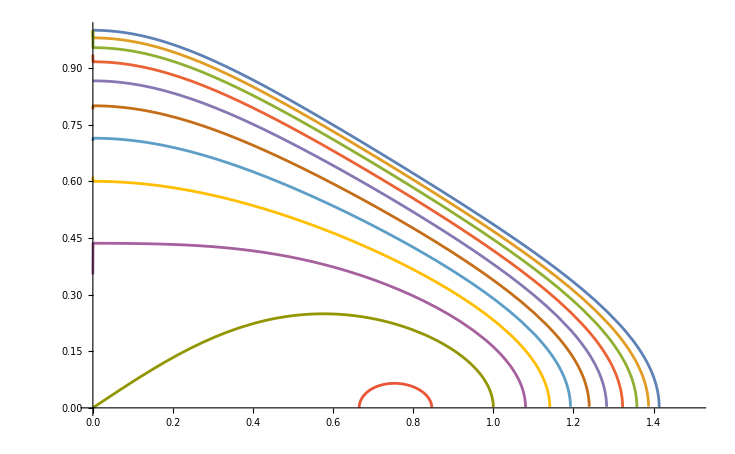

```mathematica
Plot[{andispbnog[Mc,1000000],andispbnog[Mc,10/2],andispbnog[Mc,10/3],andispbnog[Mc,10/4],andispbnog[Mc,10/5],andispbnog[Mc,10/6],andispbnog[Mc,10/7],andispbnog[Mc,10/8],andispbnog[Mc,10/9],andispbnog[Mc,10/10],andispbnog[Mc,100/109]},{Mc,0,1.5}]
```

### A = 0.6

```mathematica
Subscript[c, 2]^4 (Subscript[c, 2]^2 Subscript[k, x]^2+(γ-ⅈ U Subscript[k, x])^2) ((γ+ⅈ U Subscript[k, x])^2+Subscript[k, x]^2 Subscript[V, 1]^2) (Subscript[c, 1]^2 (γ+ⅈ U Subscript[k, x])^2+(Subscript[c, 1]^2 Subscript[k, x]^2+(γ+ⅈ U Subscript[k, x])^2) Subscript[V, 1]^2)-Subscript[c, 1]^4 (Subscript[c, 1]^2 Subscript[k, x]^2+(γ+ⅈ U Subscript[k, x])^2) ((γ-ⅈ U Subscript[k, x])^2+Subscript[k, x]^2 Subscript[V, 2]^2) (Subscript[c, 2]^2 (γ-ⅈ U Subscript[k, x])^2+(Subscript[c, 2]^2 Subscript[k, x]^2+(γ-ⅈ U Subscript[k, x])^2) Subscript[V, 2]^2)
```

```mathematica
(1/M2^2+(γ-ⅈ )^2) ((γ+ⅈ )^2+1/Ma1^2) (1/M1^2(γ+ⅈ )^2+(1/M1^2+(γ+ⅈ )^2) 1/Ma1^2)-(1+A)^2/(1-A)^2(1/M1^2 +(γ+ⅈ )^2) ((γ-ⅈ )^2+1/Ma2^2)(1/M2^2 (γ-ⅈ )^2+(1/M2^2 +(γ-ⅈ )^2) 1/Ma2^2)
```

```mathematica
(1/M2^2+(γ-ⅈ )^2) ((γ+ⅈ )^2+1/Ma1^2) (1/M1^2 1/Ma1^2+(1/M1^2+ 1/Ma1^2)(γ+ⅈ )^2)-(1+A)^2/(1-A)^2(1/M1^2 +(γ+ⅈ )^2) ((γ-ⅈ )^2+1/Ma2^2)(1/M2^2 1/Ma2^2+(1/M2^2 +1/Ma2^2) (γ-ⅈ )^2)
```

```mathematica
ReplaceAll[ (1/M2^2+(γ-ⅈ )^2) ((γ+ⅈ )^2+1/Ma1^2) (1/M1^2(γ+ⅈ )^2+(1/M1^2+(γ+ⅈ )^2) 1/Ma1^2)-(1+A)^2/(1-A)^2(1/M1^2 +(γ+ⅈ )^2) ((γ-ⅈ )^2+1/Ma2^2)(1/M2^2 (γ-ⅈ )^2+(1/M2^2 +(γ-ⅈ )^2) 1/Ma2^2),{M2->U/c2,Ma2->U/V2,M1->U/c1,Ma1->U/V1}]
```

-((1+A)^2 (V2^2/U^2+(-ⅈ+γ)^2) (c1^2/U^2+(ⅈ+γ)^2) ((c2^2 (-ⅈ+γ)^2)/U^2+(V2^2 (c2^2/U^2+(-ⅈ+γ)^2))/U^2))/(1-A)^2+(c2^2/U^2+(-ⅈ+γ)^2) (V1^2/U^2+(ⅈ+γ)^2) ((c1^2 (ⅈ+γ)^2)/U^2+(V1^2 (c1^2/U^2+(ⅈ+γ)^2))/U^2)

Set up fixed parameters for V1 and V2 c1 and c2

```mathematica
ClearAll[M1,Ma1,A,Mac,U]
```

```mathematica
(*sqrtin = √(5/3);*)
sqrtin =  √(5/3);
A=6/10;
P=1;
c1=200*sqrtin;
x1 = Solve[(c1^2-y^2)/(c1^2+y^2)==A,y];
c2 = Abs[x1[[1,1,2]]];
x2 = Solve[P*sqrtin^2==y*c1^2,y];
ρ1=x2[[1,1,2]];
x3 = Solve[P*sqrtin^2==y*c2^2,y];
ρ2=x3[[1,1,2]];
ulow = 5/100*(c1+c2)/2;
uhigh = 15/10*(c1+c2)/2;
urange = Range[ulow,uhigh,(uhigh-ulow)/100];
```

```mathematica
B= 2/10;
V1 = B/√(ρ1);
V2 = B/√(ρ2);
sols2=Table[NSolve[-((1+A)^2 (V2^2/U^2+(-ⅈ+γ)^2) ((c1)^2/U^2+(ⅈ+γ)^2) (((c2)^2 (-ⅈ+γ)^2)/U^2+(V2^2 ((c2)^2/U^2+(-ⅈ+γ)^2))/U^2))/(1-A)^2+((c2)^2/U^2+(-ⅈ+γ)^2) (V1^2/U^2+(ⅈ+γ)^2) (((c1)^2 (ⅈ+γ)^2)/U^2+(V1^2 ((c1)^2/U^2+(ⅈ+γ)^2))/U^2)==0,γ,VerifySolutions->True,WorkingPrecision->32],{U,urange}];
```

```mathematica
B= 4/10;
V1 = B/√(ρ1);
V2 = B/√(ρ2);
sols4=Table[NSolve[-((1+A)^2 (V2^2/U^2+(-ⅈ+γ)^2) ((c1)^2/U^2+(ⅈ+γ)^2) (((c2)^2 (-ⅈ+γ)^2)/U^2+(V2^2 ((c2)^2/U^2+(-ⅈ+γ)^2))/U^2))/(1-A)^2+((c2)^2/U^2+(-ⅈ+γ)^2) (V1^2/U^2+(ⅈ+γ)^2) (((c1)^2 (ⅈ+γ)^2)/U^2+(V1^2 ((c1)^2/U^2+(ⅈ+γ)^2))/U^2)==0,γ,VerifySolutions->True,WorkingPrecision->32],{U,urange}];
```

```mathematica
B= 6/10;
V1 = B/√(ρ1);
V2 = B/√(ρ2);
sols6=Table[NSolve[-((1+A)^2 (V2^2/U^2+(-ⅈ+γ)^2) ((c1)^2/U^2+(ⅈ+γ)^2) (((c2)^2 (-ⅈ+γ)^2)/U^2+(V2^2 ((c2)^2/U^2+(-ⅈ+γ)^2))/U^2))/(1-A)^2+((c2)^2/U^2+(-ⅈ+γ)^2) (V1^2/U^2+(ⅈ+γ)^2) (((c1)^2 (ⅈ+γ)^2)/U^2+(V1^2 ((c1)^2/U^2+(ⅈ+γ)^2))/U^2)==0,γ,VerifySolutions->False,WorkingPrecision->32,Method->"JenkinsTraub"],{U,urange}];
```

```mathematica
B= 8/10;
V1 = B/√(ρ1);
V2 = B/√(ρ2);
sols8=Table[NSolve[-((1+A)^2 (V2^2/U^2+(-ⅈ+γ)^2) ((c1)^2/U^2+(ⅈ+γ)^2) (((c2)^2 (-ⅈ+γ)^2)/U^2+(V2^2 ((c2)^2/U^2+(-ⅈ+γ)^2))/U^2))/(1-A)^2+((c2)^2/U^2+(-ⅈ+γ)^2) (V1^2/U^2+(ⅈ+γ)^2) (((c1)^2 (ⅈ+γ)^2)/U^2+(V1^2 ((c1)^2/U^2+(ⅈ+γ)^2))/U^2)==0,γ,VerifySolutions->True,WorkingPrecision->32],{U,urange}];
```

```mathematica
B= 100/100;
V1 = B/√(ρ1);
V2 = B/√(ρ2);
sols10=Table[NSolve[-((1+A)^2 (V2^2/U^2+(-ⅈ+γ)^2) ((c1)^2/U^2+(ⅈ+γ)^2) (((c2)^2 (-ⅈ+γ)^2)/U^2+(V2^2 ((c2)^2/U^2+(-ⅈ+γ)^2))/U^2))/(1-A)^2+((c2)^2/U^2+(-ⅈ+γ)^2) (V1^2/U^2+(ⅈ+γ)^2) (((c1)^2 (ⅈ+γ)^2)/U^2+(V1^2 ((c1)^2/U^2+(ⅈ+γ)^2))/U^2)==0,γ,VerifySolutions->True,WorkingPrecision->64],{U,urange}];
```

```mathematica
B=120/100;
V1 = B/√(ρ1);
V2 = B/√(ρ2);
sols12=Table[NSolve[-((1+A)^2 (V2^2/U^2+(-ⅈ+γ)^2) ((c1)^2/U^2+(ⅈ+γ)^2) (((c2)^2 (-ⅈ+γ)^2)/U^2+(V2^2 ((c2)^2/U^2+(-ⅈ+γ)^2))/U^2))/(1-A)^2+((c2)^2/U^2+(-ⅈ+γ)^2) (V1^2/U^2+(ⅈ+γ)^2) (((c1)^2 (ⅈ+γ)^2)/U^2+(V1^2 ((c1)^2/U^2+(ⅈ+γ)^2))/U^2)==0,γ,VerifySolutions->True,WorkingPrecision->32],{U,urange}];
```

```mathematica
gam2=Abs[Re[sols2[[All,1,1,2]]]];
gam4=Abs[Re[sols4[[All,1,1,2]]]];
gam6=Abs[Re[sols6[[All,1,1,2]]]];
gam8=Abs[Re[sols8[[All,1,1,2]]]];
gam10=Abs[Re[sols10[[All,1,1,2]]]];
gam12=Abs[Re[sols12[[All,1,1,2]]]];
Mcvals = Table[(2U)/(c1+c2),{U,urange}];
data2= Thread[{Mcvals,gam2}];
data4= Thread[{Mcvals,gam4}];
data6= Thread[{Mcvals,gam6}];
data8= Thread[{Mcvals,gam8}];
data10= Thread[{Mcvals,gam10}];data12= Thread[{Mcvals,gam12}];
```

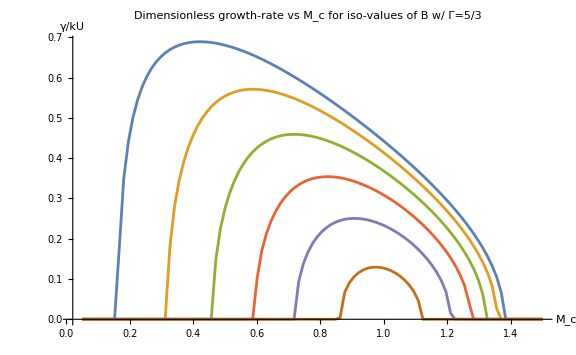

```mathematica
isoBplotadindex=ListPlot[{data2,data4,data6,data8,data10,data12},
PlotRange->Full,
Joined->True,
AxesLabel->{"M_c","γ/kU"},
PlotLabel->"Dimensionless growth-rate vs M_c for iso-values of B w/ Γ=5/3",
ImageSize->Large]
```

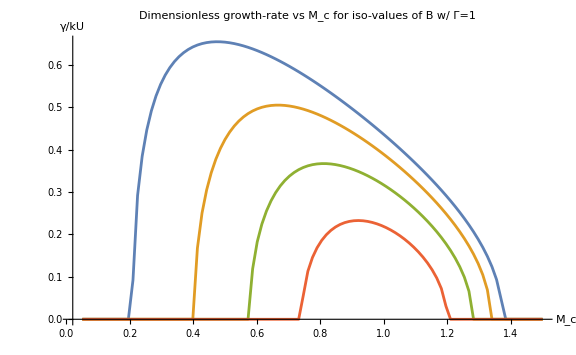

```mathematica
isoBplot=ListPlot[{data2,data4,data6,data8},
PlotRange->Full,
Joined->True,
AxesLabel->{"M_c","γ/kU"},
PlotLabel->"Dimensionless growth-rate vs M_c for iso-values of B w/ Γ=1",
ImageSize->Large]
```

```mathematica
Export["isoBplot.eps",isoBplot,"EPS"]
```

isoBplot.eps

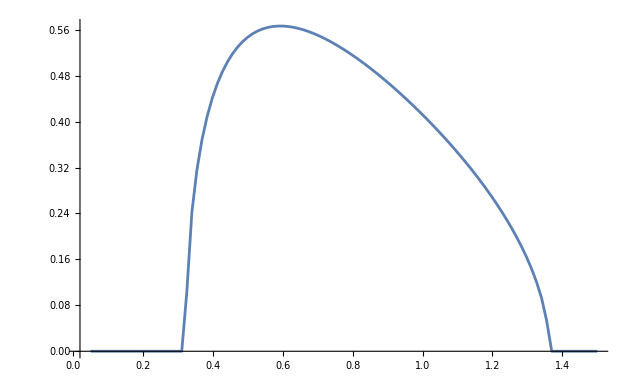

```mathematica
ListPlot[data,PlotRange->Full,Joined->True]
```

## KHI incomp w/B w/g

```mathematica
hminus = ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ1),V->B/(√(μ*ρ1)),γ̄->(γ+I*kx*U1),L->(P/ρ1)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}];
```

```mathematica
Asymptotic[ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),L->c^2/g],c->∞]//Simplify
```

-√((K^2 V^6 k_x^6+(γ̄)^6 (k_x^2+k_y^2)+3 V^2 (γ̄)^4 k_x^2 (k_x^2+k_y^2)+3 V^4 (γ̄)^2 k_x^4 (k_x^2+k_y^2))/(((γ̄)^2+V^2 k_x^2)^3))

```mathematica
Simplify[-K √((V^6 Subscript[k, x]^6+(γ̄)^6 +3 V^2 (γ̄)^4 Subscript[k, x]^2 +3 V^4 (γ̄)^2 Subscript[k, x]^4)/(((γ̄)^2+V^2 Subscript[k, x]^2)^3))]
```

-K

```mathematica
Simplify[1/2((c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2) Subscript[k, x]^2+(2 c^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2) (γ̄)^2+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2) Subscript[k, x]^2+(2 c^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2) (γ̄)^2+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2) Subscript[k, x]^2+2 (c^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4) Subscript[k, x]^2+(c^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4) Subscript[k, x]^4+(c^2) (L^2 (3 c^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2) Subscript[k, x]^4+(L^2 (3 c^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2) (γ̄)^2+c^2 K^2 V^2 Subscript[k, x]^2)^2)))]
```

1/2 ((K^2 V^4 (γ̄)^2 k_x^4+(γ̄)^6 (k_x^2+k_y^2)+2 V^2 (γ̄)^4 k_x^2 (k_x^2+k_y^2))/(K^2 L ((γ̄)^2+V^2 k_x^2)^3)-√((((γ̄)^4 (K^2 V^4 k_x^4+(γ̄)^4 (k_x^2+k_y^2)+2 V^2 (γ̄)^2 k_x^2 (k_x^2+k_y^2))^2)/L^2+(4 K^2 ((γ̄)^2+V^2 k_x^2)^3 ((γ̄)^10+c^4 K^4 V^6 k_x^6+c^4 K^2 (γ̄)^6 (k_x^2+k_y^2)+2 c^2 (γ̄)^8 (k_x^2+k_y^2)+3 c^4 K^2 V^2 (γ̄)^4 k_x^2 (k_x^2+k_y^2)+3 c^4 K^2 V^4 (γ̄)^2 k_x^4 (k_x^2+k_y^2)))/c^4)/(K^4 ((γ̄)^2+V^2 k_x^2)^6)))

```mathematica
-√((K^2 (K^4 (γ̄)^6+3 V^2 (γ̄)^4 Subscript[k, x]^2+3 V^4 (γ̄)^2 Subscript[k, x]^4+V^6 Subscript[k, x]^6))/(((γ̄)^2+V^2 Subscript[k, x]^2)^3))
```

```mathematica
ReplaceAll[-√((K^2 (K^4 (γ̄)^6+3 V^2 (γ̄)^4 Subscript[k, x]^2+3 V^4 (γ̄)^2 Subscript[k, x]^4+V^6 Subscript[k, x]^6))/(((γ̄)^2+V^2 Subscript[k, x]^2)^3)),{V->Subscript[V, 1],γ̄->Subscript[γ̄, 1]}]
```

-√((K^2 (k_x^6 V_1^6+3 k_x^4 V_1^4 (γ̄)_1^2+3 k_x^2 V_1^2 (γ̄)_1^4+K^4 (γ̄)_1^6))/((k_x^2 V_1^2+(γ̄)_1^2)^3))

```mathematica
hplus = ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))+√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ2),V->B/(√(μ*ρ2)),γ̄->(γ+I*kx*U2),L->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}];
```

```mathematica
Simplify[1/2 (√((4 K^2  ( V^6 Subscript[k, x]^6+ K^4 (γ̄)^6 +3  V^2 (γ̄)^4 Subscript[k, x]^2 +3  V^4 (γ̄)^2 Subscript[k, x]^4 ))/(((γ̄)^2+V^2 Subscript[k, x]^2)^3)))]
```

√((K^2 (K^4 (γ̄)^6+3 V^2 (γ̄)^4 k_x^2+3 V^4 (γ̄)^2 k_x^4+V^6 k_x^6))/(((γ̄)^2+V^2 k_x^2)^3))

```mathematica
ReplaceAll[√((K^2 (K^4 (γ̄)^6+3 V^2 (γ̄)^4 Subscript[k, x]^2+3 V^4 (γ̄)^2 Subscript[k, x]^4+V^6 Subscript[k, x]^6))/(((γ̄)^2+V^2 Subscript[k, x]^2)^3)),{V->Subscript[V, 2],γ̄->Subscript[γ̄, 2]}]
```

√((K^2 (k_x^6 V_2^6+3 k_x^4 V_2^4 (γ̄)_2^2+3 k_x^2 V_2^2 (γ̄)_2^4+K^4 (γ̄)_2^6))/((k_x^2 V_2^2+(γ̄)_2^2)^3))

```mathematica
K √((Subscript[k, x]^6 Subscript[V, 2]^6+3 Subscript[k, x]^4 Subscript[V, 2]^4 Subscript[γ̄, 2]^2+3 Subscript[k, x]^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^4+K^4 Subscript[γ̄, 2]^6)/((Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)^3))
```

```mathematica
disp=ReplaceAll[-(hminus (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hplus (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))+g (-ρ1+ρ2+(Subscript[γ̄, 1]^2 (P μ (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+B^2 Subscript[c, 1]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[γ̄, 1]^2)))/(μ Subscript[c, 1]^2 (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))-(Subscript[γ̄, 2]^2 (P μ (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+B^2 Subscript[c, 2]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[γ̄, 2]^2)))/(μ Subscript[c, 2]^2 (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))),{Subscript[c, 2]->√(P/ρ2),Subscript[V, 2]->B/(√(μ*ρ2)),Subscript[γ̄, 2]->(γ+I*kx*U2),Subscript[L, 2]->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2),Subscript[c, 1]->√(P/ρ1),Subscript[V, 1]->B/(√(μ*ρ1)),Subscript[γ̄, 1]->(γ+I*kx*U1),Subscript[L, 1]->(P/ρ1)/g}]
```

-(hminus ((ⅈ kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/(μ ((ⅈ kx U1+γ)^2 ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/ρ1))+(hplus ((ⅈ kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/(μ ((ⅈ kx U2+γ)^2 ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/ρ2))+g (-ρ1+((ⅈ kx U1+γ)^2 (P μ ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+(B^2 P (ky^2 (ⅈ kx U1+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ1)))/ρ1) ρ1)/(P μ ((ⅈ kx U1+γ)^2 ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/ρ1))+ρ2-((ⅈ kx U2+γ)^2 (P μ ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+(B^2 P (ky^2 (ⅈ kx U2+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ2)))/ρ2) ρ2)/(P μ ((ⅈ kx U2+γ)^2 ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/ρ2)))

```mathematica
Asymptotic[(K (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))),Subscript[c, 1]->∞]
```

(B^2 k_x^2)/(K μ)

```mathematica
Asymptotic[(Subscript[γ̄, 1]^2 (P μ (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+B^2 Subscript[c, 1]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[γ̄, 1]^2)))/(μ Subscript[c, 1]^2 (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))),Subscript[c, 1]->∞]
```

Asymptotic[((γ̄)_1^2 (P μ (K^2 V_1^2+(γ̄)_1^2) (k_y^2 V_1^2+(γ̄)_1^2)+B^2 c_1^2 ((-K^4+k_x^2 (K^2+k_y^2)) V_1^2+k_y^2 (γ̄)_1^2)))/(μ c_1^2 ((γ̄)_1^2 (K^2 V_1^2+(γ̄)_1^2) (k_y^2 V_1^2+(γ̄)_1^2)+K^2 c_1^2 (k_x^2 k_y^2 V_1^4+K^2 V_1^2 (γ̄)_1^2+(γ̄)_1^4))),c_1→∞]

```mathematica
FullSimplify[ReplaceAll[(Subscript[γ̄, 1]^2 (B^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[γ̄, 1]^2)))/(μ  (K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))),K->√(Subscript[k, x]^2+Subscript[k, y]^2)]]
```

(B^2 k_y^2 (γ̄)_1^2 (-k_y^2 V_1^2+(γ̄)_1^2))/(μ c_1^2 (k_x^2+k_y^2) (k_x^2 V_1^2+(γ̄)_1^2) (k_y^2 V_1^2+(γ̄)_1^2))

```mathematica
Asymptotic[(K (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))),Subscript[c, 2]->∞]
```

(B^2 k_x^2)/(K μ)

```mathematica
Asymptotic[(Subscript[γ̄, 2]^2 (P μ (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+B^2 Subscript[c, 2]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[γ̄, 2]^2)))/(μ Subscript[c, 2]^2 (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))),Subscript[c, 2]->∞]
```

Asymptotic[((γ̄)_2^2 (P μ (K^2 V_2^2+(γ̄)_2^2) (k_y^2 V_2^2+(γ̄)_2^2)+B^2 c_2^2 ((-K^4+k_x^2 (K^2+k_y^2)) V_2^2+k_y^2 (γ̄)_2^2)))/(μ c_2^2 ((γ̄)_2^2 (K^2 V_2^2+(γ̄)_2^2) (k_y^2 V_2^2+(γ̄)_2^2)+K^2 c_2^2 (k_x^2 k_y^2 V_2^4+K^2 V_2^2 (γ̄)_2^2+(γ̄)_2^4))),c_2→∞]

```mathematica
FullSimplify[ReplaceAll[(Subscript[γ̄, 2]^2 (B^2 Subscript[c, 2]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[γ̄, 2]^2)))/(μ Subscript[c, 2]^2 (K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))),K->√(Subscript[k, x]^2+Subscript[k, y]^2)]]
```

(B^2 k_y^2 (γ̄)_2^2 (-k_y^2 V_2^2+(γ̄)_2^2))/(μ c_2^2 (k_x^2+k_y^2) (k_x^2 V_2^2+(γ̄)_2^2) (k_y^2 V_2^2+(γ̄)_2^2))

## KHI w/o B w/ g w/ equal densities

```mathematica
Subscript[γ̄, 1]^2 (1+√(1+(4  Subscript[c, 2]^2((Subscript[k, x]^2+Subscript[k, y]^2)Subscript[c, 2]^2+ Subscript[γ̄, 2]^2))/g^2))-  Subscript[γ̄, 2]^2 (1-√(1+(4 Subscript[c, 1]^2 ((Subscript[k, x]^2+Subscript[k, y]^2)Subscript[c, 1]^2+ Subscript[γ̄, 1]^2))/g^2))=0
```

Setting equal densities and no ky

```mathematica
Subscript[γ̄, 1]^2 (1+√(1+(4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2))/g^2))- Subscript[γ̄, 2]^2 (1-√(1+(4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2))/g^2))=0
```

```mathematica
Subscript[γ̄, 1]^2 (g+√(g^2+4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2)))- Subscript[γ̄, 2]^2 (g-√(g^2+4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2)))=0
```

```mathematica
(γ+ⅈ U1 Subscript[k, x])^2 (g+√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ-ⅈ U1 Subscript[k, x])^2)))-(γ-ⅈ U1 Subscript[k, x])^2 (g-√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ+ⅈ U1 Subscript[k, x])^2)))==0
```

```mathematica
(γ+ⅈ )^2 (g/(U^2 k)+√(g^2/(U^4 Subscript[k, x]^2)+4 1/M(1/M+(γ-ⅈ )^2)))-(γ-ⅈ )^2 (g/(U1^2 Subscript[k, x])-√(g^2/(U1^4 Subscript[k, x]^2)+4 1/M (1/M +(γ+ⅈ )^2)))==0
```

```mathematica
(γ+ⅈ )^2 (1/Fr^2+√(1/Fr^4+4 1/M(1/M+(γ-ⅈ )^2)))-(γ-ⅈ )^2 (1/Fr^2-√(1/Fr^4+4 1/M (1/M +(γ+ⅈ )^2)))==0
```

Where Fr= U Sqrt(kx/g)

```mathematica
(γ+ⅈ M)^2 (L+√(L^2+4  (1+(γ-ⅈ M)^2)))-(γ-ⅈ M)^2  (L-√(L^2+4 (1+(γ+ⅈ M)^2)))==0
```

Where L = g/(c^2 k) and γ=γ/(kc)

```mathematica
(γ+ⅈ M)^2 L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))-  (γ-ⅈ M)^2 L+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2))==0
```

```mathematica
( (γ+ⅈ M)^2- (γ-ⅈ M)^2)L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2))==0
```

```mathematica
Expand[ (γ+ⅈ M)^2- (γ-ⅈ M)^2]
```

4 ⅈ M γ

```mathematica
4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2))==0
```

```mathematica
4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))==-(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2))
```

```mathematica
Solve[4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))==-(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2))]
```

```mathematica
Solve[( (γ+ⅈ M1)^2- (γ+ⅈ M2)^2)L+(γ+ⅈ M1)^2 √(L^2+4  (1+(γ+ⅈ M2)^2))+(γ+ⅈ M2)^2 √(L^2+4 (1+(γ+ⅈ M1)^2))==0,γ]
```

$Aborted

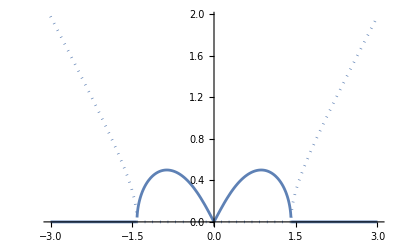

```mathematica
ReImPlot[{√(-1-M^2+√(1+4 M^2))},{M,-3,3}]
```

```mathematica
4 ⅈ M γ L+(γ+ⅈ M)^2 m==-(γ-ⅈ M)^2 p
```

Square

```mathematica
(4 ⅈ M γ L+(γ+ⅈ M)^2 m)^2==(γ-ⅈ M)^4 p^2
```

```mathematica
(4 ⅈ M γ L)^2+2*4 ⅈ M γ L*(γ+ⅈ M)^2 m+((γ+ⅈ M)^2 m)^2==(γ-ⅈ M)^4 p^2
```

```mathematica
(4 ⅈ M γ L)^2+((γ+ⅈ M)^2 m)^2-(γ-ⅈ M)^4 p^2==-2*4 ⅈ M γ L*(γ+ⅈ M)^2 m
```

Square

```mathematica
((4 ⅈ M γ L)^2+((γ+ⅈ M)^2 m)^2-(γ-ⅈ M)^4 p^2)^2==(-2*4 ⅈ M γ L*(γ+ⅈ M)^2 m)^2
```

```mathematica
Collect[ReplaceAll[((4 ⅈ M γ L)^2+((γ+ⅈ M)^2 m)^2-(γ-ⅈ M)^4 p^2)^2-(-2*4 ⅈ M γ L*(γ+ⅈ M)^2 m)^2,{m->√(L^2+4  (1+(γ-ⅈ M)^2)),p->√(L^2+4 (1+(γ+ⅈ M)^2))}],γ,Simplify]
```

-256 M^6 (L^2+(-2+M^2)^2) γ^2-512 M^4 (-4+L^2-2 M^2+2 M^4) γ^4-256 M^2 (4+L^2+4 M^2+6 M^4) γ^6-1024 (M^2+M^4) γ^8-256 M^2 γ^10

```mathematica
FullSimplify[-256 M^6 (L^2+(-2+M^2)^2) γ^2-512 M^4 (-4+L^2-2 M^2+2 M^4) γ^4-256 M^2 (4+L^2+4 M^2+6 M^4) γ^6-1024 (M^2+M^4) γ^8-256 M^2 γ^10]
```

256 γ^2 (-M^10-4 M^8 (-1+γ^2)-M^6 (4+L^2-4 γ^2+6 γ^4)-M^2 γ^4 (L^2+(2+γ^2)^2)-2 M^4 γ^2 (L^2+2 (-2+γ^2+γ^4)))

```mathematica
Collect[-M^10-4 M^8 (-1+γ^2)-M^6 (4+L^2-4 γ^2+6 γ^4)-M^2 γ^4 (L^2+(2+γ^2)^2)-2 M^4 γ^2 (L^2+2 (-2+γ^2+γ^4)),γ,Simplify]
```

-M^6 (L^2+(-2+M^2)^2)-2 M^4 (-4+L^2-2 M^2+2 M^4) γ^2-M^2 (4+L^2+4 M^2+6 M^4) γ^4-4 (M^2+M^4) γ^6-M^2 γ^8

```mathematica
-M^4 (L^2+(-2+M^2)^2)-2 M^2 (-4+L^2-2 M^2+2 M^4) γ^2- (4+L^2+4 M^2+6 M^4) γ^4-4 (1+M^2) γ^6- γ^8
```

```mathematica
Solve[-M^4 (L^2+(-2+M^2)^2)-2 M^2 (-4+L^2-2 M^2+2 M^4) γ^2- (4+L^2+4 M^2+6 M^4) γ^4-4 (1+M^2) γ^6- γ^8==0,γ]//FullSimplify
```

{{γ→-(√(-2+ⅈ L-2 M^2-√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2+ⅈ L-2 M^2-√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→-(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→-(√(-2-ⅈ L-2 M^2-√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2-ⅈ L-2 M^2-√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→-(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)}}

Try solving in one go

```mathematica
Solve[4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2))==0,γ]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γ→-(√(-2+ⅈ L-2 M^2-√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2+ⅈ L-2 M^2-√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→-(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→-(√(-2-ⅈ L-2 M^2-√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2-ⅈ L-2 M^2-√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→-(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{γ→(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)}}

```mathematica
Manipulate[ReImPlot[{(√(-2-ⅈ L-2 M^2-√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{M,-10,10}],{L,0.1,10}]
```

```mathematica
Simplify[(-M^4 (L^2+(-2+M^2)^2)-2 M^2 (-4+L^2-2 M^2+2 M^4) γ^2- (4+L^2+4 M^2+6 M^4) γ^4-4 (1+M^2) γ^6- γ^8)/(γ-(√(-2+ⅈ L-2 M^2-√(-(2 ⅈ+L)^2+16 M^2)))/(√2))]
```

(2 (M^8+4 M^6 (-1+γ^2)+M^4 (4+L^2-4 γ^2+6 γ^4)+γ^4 (L^2+(2+γ^2)^2)+2 M^2 γ^2 (L^2+2 (-2+γ^2+γ^4))))/(√2 √(-2+ⅈ L-2 M^2-√(4-4 ⅈ L-L^2+16 M^2))-2 γ)

```mathematica
Manipulate[{N[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)-(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)],N[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)],N[(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)]},{M,-3,3},{L,0,1}]
```

```mathematica
Manipulate[{N[ReplaceAll[4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2)),γ->(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)],{50,50}],N[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)],N[ReplaceAll[4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2)),γ->(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)],{50,50}],N[(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)]},{M,-30,30},{L,0,1}]
```

```mathematica
Manipulate[{N[ReplaceAll[4 ⅈ M S γ L+(γ+ⅈ M S)^2 √(L^2+4  (1+(γ-ⅈ M S)^2))+(γ-ⅈ M S)^2 √(L^2+4 (1+(γ+ⅈ M S)^2)),γ->(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)],{50,50}],N[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)],N[ReplaceAll[4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2)),γ->(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)],{50,50}],N[(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)]},{M,-30,30},{L,0,1},{S,-1,1}]
```

```mathematica
N[10/50000^2]
```

4.×10^-9

```mathematica
Collect[ReplaceAll[4 ⅈ M γ L+(γ+ⅈ M)^2 √(L^2+4  (1+(γ-ⅈ M)^2))+(γ-ⅈ M)^2 √(L^2+4 (1+(γ+ⅈ M)^2))==0,γ->(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)],γ]
```

2 ⅈ √2 L M √(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2))+(ⅈ M+(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2))^2 √(L^2+4 (1+(-ⅈ M+(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2))^2))+(-ⅈ M+(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2))^2 √(L^2+4 (1+(ⅈ M+(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2))^2))==0

```mathematica
Manipulate[ReImPlot[{(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)-(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2)},{M,-10,10}],{L,0.1,10}]
```

```mathematica
Asymptotic[(√(-2-ⅈ L-2 M^2+√(-(-2 ⅈ+L)^2+16 M^2)))/(√2),{M,-∞,3}]
```

ⅈ+(ⅈ (-2+2 ⅈ L+L^2))/(16 M^3)-(ⅈ (-4+4 ⅈ L+L^2))/(32 M^2)-L/(4 M)+ⅈ M

```mathematica
Asymptotic[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2),{M,-∞,3}]
```

ⅈ+(ⅈ (-2-2 ⅈ L+L^2))/(16 M^3)-(ⅈ (-4-4 ⅈ L+L^2))/(32 M^2)+L/(4 M)+ⅈ M

```mathematica
√(-1+ⅈ L/2- M^2+1/2 √(-(2 ⅈ+L)^2+16 M^2))
```

```mathematica
√(-1+ⅈ L/2- M^2+√(( 1-ⅈ L/2)^2+4 M^2))
```

```mathematica
√(-(1-ⅈ L/2)- M^2+√(( 1-ⅈ L/2)^2+4 M^2))
```

```mathematica
√(-((1-ⅈ L/2)+ M^2)+√(( 1-ⅈ L/2)^2+4 M^2))
```

```mathematica
ⅈ √((1-ⅈ L/2)+ M^2-√(( 1-ⅈ L/2)^2+4 M^2))
```

```mathematica
Asymptotic[√(-(1-ⅈ L/2)- M^2+√(( 1-ⅈ L/2)^2+4 M^2)),{M,∞,3}]
```

-ⅈ+(ⅈ (-2-2 ⅈ L+L^2))/(16 M^3)+(ⅈ (-4-4 ⅈ L+L^2))/(32 M^2)+L/(4 M)+ⅈ M

```mathematica
Asymptotic[√(-(1+ⅈ L/2)- M^2+√(( 1+ⅈ L/2)^2+4 M^2)),{M,∞,3}]
```

-ⅈ+(ⅈ (-2+2 ⅈ L+L^2))/(16 M^3)+(ⅈ (-4+4 ⅈ L+L^2))/(32 M^2)-L/(4 M)+ⅈ M

```mathematica
Manipulate[{N[√(-(1-ⅈ L/2)- M^2+√(( 1-ⅈ L/2)^2+4 M^2))],N[-I*(1+M)],N[-I*(-1+M)]},{M,0.1,20},{L,0.1,10}]
```

```mathematica
Solve[-1(((1-ⅈ 1/(2L))+ M^2)-√(( 1-ⅈ 1/(2L))^2+4 M^2))==0,M]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{M→0},{M→-(√(ⅈ+2 L))/(√L)},{M→(√(ⅈ+2 L))/(√L)}}

```mathematica
Solve[-1(((1-ⅈ L/2)+ M^2)-√(( 1-ⅈ L/2)^2+4 M^2))==0,L]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{L→-ⅈ (-2+M^2)}}

```mathematica
Solve[√(-1(((1+ⅈ L/2)+ M^2)-√(( 1+ⅈ L/2)^2+4 M^2)))==0,M]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{M→0},{M→-√(2-ⅈ L)},{M→√(2-ⅈ L)}}

```mathematica
ReplaceAll[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2),M->√2]//Simplify
```

(√(-6+ⅈ L+√(32-(2 ⅈ+L)^2)))/(√2)

```mathematica
Manipulate[N[(√(-6+ⅈ L+√(32-(2 ⅈ+L)^2)))/(√2)],{L,0,0.1}]
```

```mathematica
Manipulate[ReImPlot[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2),{M,-3,3}],{L,0,1}]
```

```mathematica
Manipulate[N[(√(-2+ⅈ L-2 M^2+√(-(2 ⅈ+L)^2+16 M^2)))/(√2)],{M,-3,3},{L,0.001,1}]
```

```mathematica
√(-1+ⅈ L/2- M^2+√(( 1-(I L)/2)^2+4 M^2))
```

```mathematica
√(-1(1-ⅈ L/2)- M^2+√(( 1-(I L)/2)^2+4 M^2))
```

```mathematica
Manipulate[N[√(-1(1-ⅈ L/2)- M^2+√(( 1-(I L)/2)^2+4 M^2))],{M,-3,3},{L,0.001,1}]
```

```mathematica
Manipulate[N[√(-1(((1-ⅈ L/2)+ M^2)-√(( 1-ⅈ L/2)^2+4 M^2)))],{M,-3,3},{L,0.001,1}]
```

```mathematica
Manipulate[ReImPlot[√(-1(((1-ⅈ L/2)+ M^2)-√(( 1-ⅈ L/2)^2+4 M^2))),{M,-3,3}],{L,0,1}]
```

```mathematica
Normal[Series[√(-1(((1-ⅈ L/2)+ M^2)-√(( 1-ⅈ L/2)^2+4 M^2))),{M,∞,1}]]
```

-ⅈ+L/(4 M)+ⅈ M

```mathematica
Normal[Series[√(-1(((1-ⅈ L/2)+ M^2)-√(( 1-ⅈ L/2)^2+4 M^2))),{M,-∞,1}]]
```

ⅈ+L/(4 M)+ⅈ M

```mathematica
Manipulate[{N[L/(4Abs[ M])+ⅈ( Abs[M]-1)],N[√(-1(((1-ⅈ L/2)+ M^2)-√(( 1-ⅈ L/2)^2+4 M^2)))]},{M,-100,100},{L,0.00000001,1}]
```

```mathematica
Manipulate[ReImPlot[√(-1(((1+ⅈ L/2)+ M^2)-√(( 1+ⅈ L/2)^2+4 M^2))),{M,-3,3}],{L,0.0000001,1}]
```

```mathematica
Asymptotic[-√(-1(((1+ⅈ L/2)+ M^2)-√(( 1+ⅈ L/2)^2+4 M^2))),{M,∞,2}]
```

ⅈ+ⅈ/(8 M^2)+L/(8 M^2)-(ⅈ L^2)/(32 M^2)+L/(4 M)-ⅈ M

```mathematica
Asymptotic[-√(-1(((1+ⅈ L/2)+ M^2)-√(( 1+ⅈ L/2)^2+4 M^2))),{M,-∞,2}]
```

-ⅈ-ⅈ/(8 M^2)-L/(8 M^2)+(ⅈ L^2)/(32 M^2)+L/(4 M)-ⅈ M

```mathematica
Series[√(-1(((1+ⅈ L/2)+ M^2)-√(( 1+ⅈ L/2)^2+4 M^2))),{M,-∞,2}]
```

ⅈ M+ⅈ-L/(4 M)-(ⅈ (-4+4 ⅈ L+L^2))/(32 M^2)+O[1/M]^3

```mathematica
Manipulate[{N[L/(4 M)-ⅈ( M-1)],N[√(-1(((1+ⅈ L/2)+ M^2)-√(( 1+ⅈ L/2)^2+4 M^2)))],N[L/(4 M)-ⅈ (M+1)]},{M,-100,100},{L,0.00000001,1}]
```

```mathematica
Manipulate[{N[L/(4 Abs[M])-ⅈ( Abs[M]-1)],N[√(-1(((1+ⅈ L/2)+ M^2)-√(( 1+ⅈ L/2)^2+4 M^2)))]},{M,-100,100},{L,0.00000001,1}]
```

```mathematica
Manipulate[Plot[Re[I √((1-ⅈ L/2)+ M^2-√(( 1-ⅈ L/2)^2+4 M^2))],{M,-3,3}],{L,0.001,1}]
```

Try solving in one go

```mathematica
ReplaceAll[ Subscript[γ̄, 1]^2 (g+√(g^2+4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2)))- Subscript[γ̄, 2]^2 (g-√(g^2+4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2))), {Subscript[γ̄, 1]->(γ+I*Subscript[k, x] U1), Subscript[γ̄, 2]->(γ-I*Subscript[k, x] U1)}]
```

(γ+ⅈ U1 k_x)^2 (g+√(g^2+4 c^2 (c^2 k_x^2+(γ-ⅈ U1 k_x)^2)))-(γ-ⅈ U1 k_x)^2 (g-√(g^2+4 c^2 (c^2 k_x^2+(γ+ⅈ U1 k_x)^2)))

```mathematica
Solve[(γ+ⅈ U1 Subscript[k, x])^2 (g+√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ-ⅈ U1 Subscript[k, x])^2)))-(γ-ⅈ U1 Subscript[k, x])^2 (g-√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ+ⅈ U1 Subscript[k, x])^2)))==0,γ]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γ→-(√(-k_x (-ⅈ g+2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (-ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)},{γ→(√(-k_x (-ⅈ g+2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (-ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)},{γ→-(√(k_x (ⅈ g-2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (-ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)},{γ→(√(k_x (ⅈ g-2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (-ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)},{γ→-(√(-k_x (ⅈ g+2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)},{γ→(√(-k_x (ⅈ g+2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)},{γ→-(√(k_x (-ⅈ g-2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)},{γ→(√(k_x (-ⅈ g-2 (c^2+U1^2) k_x+√(-g^2+4 c^2 k_x (ⅈ g+(c^2+4 U1^2) k_x)))))/(√2)}}

## Testing analytic expression w/o B w/g in lab frame

```mathematica
(γ+ⅈ U1 Subscript[k, x])^2 (g+√(g^2+4 c^2 (c^2 k^2+(γ+ⅈ U2 Subscript[k, x])^2)))-(γ+ⅈ U2 Subscript[k, x])^2 (g-√(g^2+4 c^2 (c^2 k^2+(γ+ⅈ U1 Subscript[k, x])^2)))==0
```

```mathematica
Solve[(γ+ⅈ U1 k)^2 (g+√(g^2+4 c^2 (c^2 k^2+(γ+ⅈ U2 k)^2)))-(γ+ⅈ U2 k)^2 (g-√(g^2+4 c^2 (c^2 k^2+(γ+ⅈ U1 k)^2)))==0,γ]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γ→-1/2 ⅈ (k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k U1^2+2 √(-g^2+4 ⅈ c^2 g k+4 c^2 k^2 (c^2+(U1-U2)^2))-2 k U1 U2+k U2^2)))},{γ→1/2 ⅈ (-k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k U1^2+2 √(-g^2+4 ⅈ c^2 g k+4 c^2 k^2 (c^2+(U1-U2)^2))-2 k U1 U2+k U2^2)))},{γ→-1/2 ⅈ (k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k U1^2-2 √(-g^2+4 ⅈ c^2 g k+4 c^2 k^2 (c^2+(U1-U2)^2))-2 k U1 U2+k U2^2)))},{γ→1/2 ⅈ (-k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k U1^2-2 √(-g^2+4 ⅈ c^2 g k+4 c^2 k^2 (c^2+(U1-U2)^2))-2 k U1 U2+k U2^2)))},{γ→-1/2 ⅈ (k (U1+U2)+√(-2 ⅈ g k+4 c^2 k^2+k^2 U1^2-2 ⅈ √(k^2 (g^2+4 ⅈ c^2 g k-4 c^2 k^2 (c^2+(U1-U2)^2)))-2 k^2 U1 U2+k^2 U2^2))},{γ→1/2 ⅈ (-k (U1+U2)+√(-2 ⅈ g k+4 c^2 k^2+k^2 U1^2-2 ⅈ √(k^2 (g^2+4 ⅈ c^2 g k-4 c^2 k^2 (c^2+(U1-U2)^2)))-2 k^2 U1 U2+k^2 U2^2))},{γ→-1/2 ⅈ (k (U1+U2)+√(-2 ⅈ g k+4 c^2 k^2+k^2 U1^2+2 ⅈ √(k^2 (g^2+4 ⅈ c^2 g k-4 c^2 k^2 (c^2+(U1-U2)^2)))-2 k^2 U1 U2+k^2 U2^2))},{γ→1/2 ⅈ (-k (U1+U2)+√(-2 ⅈ g k+4 c^2 k^2+k^2 U1^2+2 ⅈ √(k^2 (g^2+4 ⅈ c^2 g k-4 c^2 k^2 (c^2+(U1-U2)^2)))-2 k^2 U1 U2+k^2 U2^2))}}

Try 1

```mathematica
Simplify[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]-√((U1 Subscript[k, x]+U2 Subscript[k, x])^2+2 (-ⅈ g Subscript[k, x]+2 c^2 Subscript[k, x]^2-2 U1 U2 Subscript[k, x]^2+Subscript[k, x] √(-g^2-4 ⅈ c^2 g Subscript[k, x]+4 c^4 Subscript[k, x]^2+4 c^2 U1^2 Subscript[k, x]^2-8 c^2 U1 U2 Subscript[k, x]^2+4 c^2 U2^2 Subscript[k, x]^2))))]
```

-1/2 ⅈ (U1 k_x+U2 k_x+√(k_x ((4 c^2+(U1-U2)^2) k_x+2 (-ⅈ g+√(-g^2-4 ⅈ c^2 g k_x+4 c^2 (c^2+(U1-U2)^2) k_x^2)))))

```mathematica
-1/2 ⅈ (U1 Subscript[k, x]+U2 Subscript[k, x]+√(Subscript[k, x] ((4 c^2+(U1-U2)^2) Subscript[k, x]+2 (-ⅈ g+√(-g^2-4 ⅈ c^2 g Subscript[k, x]+4 c^2 (c^2+(U1-U2)^2) Subscript[k, x]^2)))))
```

```mathematica
-1/2 ⅈ (U1 Subscript[k, x]+U2 Subscript[k, x]+√(Subscript[k, x] ((4 c^2+(U1-U2)^2) Subscript[k, x]+2 (-ⅈ g+Subscript[k, x] c √(-g^2/(c^2 Subscript[k, x]^2)-(4 ⅈ  g)/Subscript[k, x]+4  (c^2+(U1-U2)^2))))))
```

```mathematica
-1/2 ⅈ (U1 Subscript[k, x]+U2 Subscript[k, x]+√(Subscript[k, x] ((4 c^2+(U1-U2)^2) Subscript[k, x]+2 (-ⅈ g+Subscript[k, x] c^2 4 √(-g^2/(16 c^4 Subscript[k, x]^2)-(ⅈ  g)/(4 c^2 Subscript[k, x])+  1/4+((U1-U2)/(2c))^2)))))
```

```mathematica
-1/2 ⅈ (U1 Subscript[k, x]+U2 Subscript[k, x]+√(Subscript[k, x] ((4 c^2+(U1-U2)^2) Subscript[k, x]+2 Subscript[k, x] c^2(-ⅈ 1/L+ 4 √(-1/(16 L^2)-ⅈ/(4L)+  1/4+(Mc)^2)))))
```

```mathematica
-Subscript[k, x]/2 ⅈ (U1 +U2 +√(4 c^2(1+(U1-U2)^2/(4 c^2))+2 c^2(-ⅈ 1/L+ 4 √(-1/(16 L^2)-ⅈ/(4L)+  1/4+(Mc)^2))))
```

```mathematica
-(Subscript[k, x] c)/2 ⅈ (M1 +M2 +√(4+4 Mc^2-ⅈ 2/L+ 16 √(-1/(4 L^2)-ⅈ/L+  1+4(Mc)^2)))
```

```mathematica
-(Subscript[k, x] c)/2 ⅈ (M1 +M2 +√(4(1+Mc^2-ⅈ 1/(2L)+ 4 √((1-ⅈ/(2L))^2+4 Mc^2))))
```

```mathematica
-(Subscript[k, x] c)/2 ⅈ (M1 +M2 +2 √((1-ⅈ 1/(2L))+Mc^2+ 4 √((1-ⅈ/(2L))^2+4 Mc^2)))
```

Try 2

```mathematica
-1/2 ⅈ (k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k U1^2-2 √(-g^2+4 ⅈ c^2 g k+4 c^2 k^2 (c^2+(U1-U2)^2))-2 k U1 U2+k U2^2)))
```

```mathematica
-1/2 ⅈ (k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k U1^2-2 k U1 U2+k U2^2-2 √(-g^2+4 ⅈ c^2 g k+4 c^4 k^2 (1+4 Mc^2)))))
```

```mathematica
-1/2 ⅈ (k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k U1^2-2 k U1 U2+k U2^2-4 c^2 k √(-g^2/(4 c^4 k^2)+(ⅈ  g)/(c^2 k)+1+4 Mc^2))))
```

```mathematica
-1/2 ⅈ (k (U1+U2)+√(k (2 ⅈ g+4 c^2 k+k (U1-U2)^2-4 c^2 k √(-1/(4 L^2)+ⅈ/L+1+4 Mc^2))))
```

```mathematica
-1/2 ⅈ (k (U1+U2)+2 c k √((ⅈ g)/(2 c^2 k)+1+(k (U1-U2)^2)/(4 c^2 k)-√(-1/(4 L^2)+ⅈ/L+1+4 Mc^2)))
```

```mathematica
- c k  ⅈ ( (M1+M2)/2+√((1+ⅈ/(2 L))+Mc^2-√((1+ⅈ/(2L))^2+4 Mc^2)))
```

```mathematica
Series[-  ⅈ ( (M1+M2)/2+√((1+ⅈ/(2 L))+(M1-M2)^2-√((1+ⅈ/(2L))^2+4(M1-M2)^2))),{M2,∞,2}]//Simplify
```

-(3 ⅈ M2)/2+1/2 ⅈ (2+M1)+1/(4 L M2)+(-ⅈ+4 ⅈ L^2+L (4+8 M1))/(32 L^2 M2^2)+O[1/M2]^3

```mathematica
(1+M1)*i
```

## Testing Altered Dispersion Relation

New dispersion relation is

```mathematica
(hplus (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2))/(K^2 Subscript[c, 2]^2 Subscript[k, x]^2 Subscript[V, 2]^2+K^2 (Subscript[c, 2]^2+Subscript[V, 2]^2) Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)-(hminus (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2))/(K^2 Subscript[c, 1]^2 Subscript[k, x]^2 Subscript[V, 1]^2+K^2 (Subscript[c, 1]^2+Subscript[V, 1]^2) Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)+g ((K^2 P μ Subscript[k, x]^2 Subscript[V, 2]^2+(K^2 P μ+B^2 Subscript[k, y]^2) Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 Subscript[k, x]^2 Subscript[V, 2]^2+K^2 (Subscript[c, 2]^2+Subscript[V, 2]^2) Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)-(K^2 P μ Subscript[k, x]^2 Subscript[V, 1]^2+(K^2 P μ+B^2 Subscript[k, y]^2) Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 Subscript[k, x]^2 Subscript[V, 1]^2+K^2 (Subscript[c, 1]^2+Subscript[V, 1]^2) Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))==0
```

```mathematica
ReplaceAll[(hplus (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2))/(K^2 Subscript[c, 2]^2 Subscript[k, x]^2 Subscript[V, 2]^2+K^2 (Subscript[c, 2]^2+Subscript[V, 2]^2) Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)-(hminus (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2))/(K^2 Subscript[c, 1]^2 Subscript[k, x]^2 Subscript[V, 1]^2+K^2 (Subscript[c, 1]^2+Subscript[V, 1]^2) Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)+g ((K^2 P μ Subscript[k, x]^2 Subscript[V, 2]^2+(K^2 P μ+B^2 Subscript[k, y]^2) Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 Subscript[k, x]^2 Subscript[V, 2]^2+K^2 (Subscript[c, 2]^2+Subscript[V, 2]^2) Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)-(K^2 P μ Subscript[k, x]^2 Subscript[V, 1]^2+(K^2 P μ+B^2 Subscript[k, y]^2) Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 Subscript[k, x]^2 Subscript[V, 1]^2+K^2 (Subscript[c, 1]^2+Subscript[V, 1]^2) Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)),{Subscript[V, 1]->0,Subscript[V, 2]->0,B->0}]
```

-(hminus P μ (γ̄)_1^4)/(K^2 c_1^2 (γ̄)_1^2+(γ̄)_1^4)+(hplus P μ (γ̄)_2^4)/(K^2 c_2^2 (γ̄)_2^2+(γ̄)_2^4)+g (-(K^2 P μ (γ̄)_1^2)/(K^2 c_1^2 (γ̄)_1^2+(γ̄)_1^4)+(K^2 P μ (γ̄)_2^2)/(K^2 c_2^2 (γ̄)_2^2+(γ̄)_2^4))

```mathematica
-(hminus P  Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 +Subscript[γ̄, 1]^2)+(hplus P  Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2)+g (-(K^2 P)/(K^2 Subscript[c, 1]^2 +Subscript[γ̄, 1]^2)+(K^2 P)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2))
```

```mathematica
-(hminus   Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 +Subscript[γ̄, 1]^2)+(hplus   Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2)+g (-K^2/(K^2 Subscript[c, 1]^2 +Subscript[γ̄, 1]^2)+K^2/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2))
```

Old dispersion relation is

```mathematica
-(hminus (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hplus (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))+g (-Subscript[ρ, 1]+Subscript[ρ, 2]+(Subscript[γ̄, 1]^2 (P μ (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+B^2 Subscript[c, 1]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[γ̄, 1]^2)))/(μ Subscript[c, 1]^2 (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))-(Subscript[γ̄, 2]^2 (P μ (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+B^2 Subscript[c, 2]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[γ̄, 2]^2)))/(μ Subscript[c, 2]^2 (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))))
```

```mathematica
ReplaceAll[-(hminus (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hplus (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))+g (-Subscript[ρ, 1]+Subscript[ρ, 2]+(Subscript[γ̄, 1]^2 (P μ (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+B^2 Subscript[c, 1]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[γ̄, 1]^2)))/(μ Subscript[c, 1]^2 (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))-(Subscript[γ̄, 2]^2 (P μ (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+B^2 Subscript[c, 2]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[γ̄, 2]^2)))/(μ Subscript[c, 2]^2 (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))),{Subscript[V, 1]->0,Subscript[V, 2]->0,B->0}]
```

-(hminus P (γ̄)_1^6)/(K^2 c_1^2 (γ̄)_1^4+(γ̄)_1^6)+(hplus P (γ̄)_2^6)/(K^2 c_2^2 (γ̄)_2^4+(γ̄)_2^6)+g (-ρ_1+ρ_2+(P (γ̄)_1^6)/(c_1^2 (K^2 c_1^2 (γ̄)_1^4+(γ̄)_1^6))-(P (γ̄)_2^6)/(c_2^2 (K^2 c_2^2 (γ̄)_2^4+(γ̄)_2^6)))

```mathematica
-(hminus P Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 +Subscript[γ̄, 1]^2)+(hplus P Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2)+g (-Subscript[ρ, 1]+Subscript[ρ, 2]+(P Subscript[γ̄, 1]^2)/(Subscript[c, 1]^2 (K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2))-(P Subscript[γ̄, 2]^2)/(Subscript[c, 2]^2 (K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2)))
```

```mathematica
-(hminus P Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 +Subscript[γ̄, 1]^2)+(hplus P Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2)+g (-Subscript[ρ, 1]+Subscript[ρ, 2]+(Subscript[ρ, 1] Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2)-(Subscript[ρ, 2] Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2))
```

```mathematica
-(hminus P Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 +Subscript[γ̄, 1]^2)+(hplus P Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2)+g (Together[-Subscript[ρ, 1]+(Subscript[ρ, 1] Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2)]+Together[Subscript[ρ, 2]-(Subscript[ρ, 2] Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 +Subscript[γ̄, 2]^2)])
```

-(hminus P (γ̄)_1^2)/(K^2 c_1^2+(γ̄)_1^2)+(hplus P (γ̄)_2^2)/(K^2 c_2^2+(γ̄)_2^2)+g (-(K^2 c_1^2 ρ_1)/(K^2 c_1^2+(γ̄)_1^2)+(K^2 c_2^2 ρ_2)/(K^2 c_2^2+(γ̄)_2^2))

```mathematica
-(hminus  Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2)+(hplus  Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2+Subscript[γ̄, 2]^2)+g (-(K^2 Subscript[c, 1]^2 Subscript[ρ, 1])/(P(K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2))+(K^2 Subscript[c, 2]^2 Subscript[ρ, 2])/(P(K^2 Subscript[c, 2]^2+Subscript[γ̄, 2]^2)))
```

```mathematica
-(hminus  Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2)+(hplus  Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2+Subscript[γ̄, 2]^2)+g (-(K^2 Subscript[c, 1]^2)/(Subscript[c, 1]^2 (K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2))+(K^2 Subscript[c, 2]^2)/(Subscript[c, 2]^2 (K^2 Subscript[c, 2]^2+Subscript[γ̄, 2]^2)))
```

```mathematica
-(hminus  Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2)+(hplus  Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2+Subscript[γ̄, 2]^2)+g (-K^2/(K^2 Subscript[c, 1]^2+Subscript[γ̄, 1]^2)+K^2/(K^2 Subscript[c, 2]^2+Subscript[γ̄, 2]^2))
```

Hence they are equivalent in the no B limit